# MathematicaMCMC

Author:
Mario A. Rodríguez-Meza
Instituto Nacional de Investigaciones Nucleares
marioalberto.rodriguez@inin.gob.mx
Ciudad de México. January 1st, 2019; 
Updated: 2020-11-5

Acknowledgements: Tula Bernal, Lizbeth M. Fernández-Hernández and Ariadna Montiel 

Based on a Mathematica code shared by Tula Bernal

Paper reference: 
If you use this code please cite the reference: 

Lizbeth M. Fernández-Hernández, Ariadna Montiel and Mario A. Rodríguez-Meza, MNRAS, 488, 5127-5144 (2019). arXiv:1809.06875. (See the bibtex file format: citation_paper.bibtex)

RUN:  shift-enter on the biggest right bracket →
It runs in about one minute.

OUPUT:
- LaTex files:
When finished you will have two tex files in Results/ dir: all.tex and PISO_parameters.tex
copy the lines in all.tex and paste them into the PISO_parameters.tex after where it says:
%
%Insert here each galaxy parameter line
%
 
 LaTex it and you will have the table of the parameters results.

- TXT file parameter files:  PISO_parameters.txt and all.txt files are the same data as in the TEX files but in plain format.

- Chains in file:
Results/Chains/IC2574_PISO-MCExt.txt
can be processed using GetDist:

In a terminal:
$ python getdist-plots_and_stat.py > stat_output

Or run jupyter:
$ jupyter notebook

and in the web browser open the file “getdist-plots_and_stat.ipynb” and run the notebook. The confidence regions and posteriors files will be in the getdist_analysis directory.

## Readme

Case study: 
rotation curve galaxy IC 2574; 
data from SPARC catalog, F. Lelli et al., Astron. J. 152, 157 (2016); 
implemented model Pseudo isothermal dark matter density profile;
two parameters: ρ_s and r_s. You can change the model in section 30.a.

For a different two parameter density profile model make the appropriate changes in subsubsubsection 30.a Equations Rotation curve dark matter model.

For a different rotation curve data, change the line:

RCTable=Import["IC2574_rotmod.txt","Data"];

in the subsubsection 30.b.1 Input galaxy rotation curve data. Make sure the column types correspond to:

(* From de header of the data file: IC2574_rotmod_header.txt :
# Distance=3.91 Mpc
# Rad Vobs errV Vgas Vdisk Vbul SBdisk SBbul
# kpc km/s km/s km/s km/s km/s L/pc^2 L/pc^2
*)

Columns in the chain extended file (to process using GetDist)
(* 
col1: weights, 
col2: -2LogLike, 
col3: ρs (fit parameter),
col4: rs (fit parameter),
col5: muDM (derived parameter),
col6: m300 (derived parameter),
col7: mTot (DM) (derived parameter),
col8: %mTot (DM) (derived parameter)
*)

Input parameters:
Section 30.e.2
nc1=30000; number random walks in chain 1
nc2=30000; number random walks in chain 2

Section 30.e.3
nth=1;  fresh MCMC compution. If nth=2, read chains from files and start from the end of the chains.
δ=0.1;  control the size of the random walk.

In the general section of MCMC Modules (i.4):
MarkovChainProcessing2[fileNameMC1_,fileNameMC2_,np_,nt_,fb_]
np is number of parameters
nt is and integer to thinning the chains
fb is the burning factor

Output:
Folder Results
Folder Results/Chains, the two chains files, it can be used GetDist to analyse them.
Folder Results/LaTeX, parameters and derived values in LaTeX format.
Folder Results/PDF, pdf file of rotation curve plot. 
Folder Results/TXT, parameters and derived quantities values in plain format

Changes basically only in section or subsections with "(adapt to your needs)"

## i.1 Init Mathematica and fitting modules

## 1 Some startup steps...

```mathematica
Clear["Global`*"];
```

```mathematica
taall=AbsoluteTime[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Off[InterpolatingFunction::dmval]
Off[General::obspkg]
Off[DeleteFile::fdnfnd]
Off[NonlinearModelFit::sszero]
Off[General::munfl]
Off[CreateDirectory::filex]
```

```mathematica
<<ErrorBarPlots`
```

## 2 Directories and files

```mathematica
(*If you don.b4t have a Results directory tree, it will created in the place where the notebook is*)
```

```mathematica
rootStrDir="Results";
PDFStr=rootStrDir<>"/PDF";
TXTStr=rootStrDir<>"/TXT";
LaTeXStr=rootStrDir<>"/LaTeX";
ChainsStr=rootStrDir<>"/Chains";
TablesStr=rootStrDir<>"/Tables";
getdistDirStr=rootStrDir<>"/getdist_analysis";
posteriorsDirStr=getdistDirStr<>"/posteriors";
confidenceRegionsDirStr=getdistDirStr<>"/confidenceRegions";
```

```mathematica
allTeX="/all.tex";
allTXT="/all.txt";
```

```mathematica
newRun=False; (*use True UNDER YOUR OWN RISK!!! 
Make True to renew folder Results/ False*)
If[newRun,DeleteDirectory["Results",DeleteContents->True];
CreateDirectory["Results"];
CreateDirectory[rootStrDir];
CreateDirectory[PDFStr];
CreateDirectory[TXTStr];
CreateDirectory[LaTeXStr];
CreateDirectory[ChainsStr];
CreateDirectory[TablesStr];
CreateDirectory[getdistDirStr];
CreateDirectory[posteriorsDirStr];
CreateDirectory[confidenceRegionsDirStr];
]
```

```mathematica
commandstringDir="if [ ! -d Results ]; then mkdir Results; fi";
Run[commandstringDir]
commandstringDirroot="if [ ! -d "<>rootStrDir <>" ]; then mkdir "<>rootStrDir<>"; fi";
Run[commandstringDirroot]
commandstringDirPDF="if [ ! -d "<>PDFStr <>" ]; then mkdir "<>PDFStr<>"; fi";
Run[commandstringDirPDF]

commandstringDirroot="if [ ! -d "<>TXTStr <>" ]; then mkdir "<>TXTStr<>"; fi";
Run[commandstringDirroot]

commandstringDirroot="if [ ! -d "<>LaTeXStr <>" ]; then mkdir "<>LaTeXStr<>"; fi";
Run[commandstringDirroot]

commandstringDirroot="if [ ! -d "<>ChainsStr <>" ]; then mkdir "<>ChainsStr<>"; fi";
Run[commandstringDirroot]

commandstringDirroot="if [ ! -d "<>TablesStr <>" ]; then mkdir "<>TablesStr<>"; fi";
Run[commandstringDirroot]

commandstringDirroot="if [ ! -d "<>getdistDirStr <>" ]; then mkdir "<>getdistDirStr<>"; fi";
Run[commandstringDirroot]

commandstringDirroot="if [ ! -d "<>posteriorsDirStr <>" ]; then mkdir "<>posteriorsDirStr<>"; fi";
Run[commandstringDirroot]

commandstringDirroot="if [ ! -d "<>confidenceRegionsDirStr <>" ]; then mkdir "<>confidenceRegionsDirStr<>"; fi";
Run[commandstringDirroot]
```

0

0

0

«7 more identical outputs»

## 3 Modules definitions

### 1. Set general parameters and plot styles and modules

#### PlotStyle parameters

```mathematica
ImageSizePlot=400;
```

```mathematica
Dashing1=Dashing[Tiny]; (*Dots*)
Dashing2=Dashing[Large]; (*Normal dashing*)
Dashing3=Dashing[{.05,.015}]; (*Long dashing*)
Dashing4=Dashed;(*Small dashing*)
Dashing5=DotDashed;
```

```mathematica
plotMarker1="○";
plotMarker2="□";
plotMarker3="◇";
plotMarker4="△";
plotMarker5="▽";
plotMarker6="•";
plotMarker7="■";
plotMarker8="◆";
plotMarker9="▲";
plotMarker10="▼";
```

```mathematica
lineThickness1=Thickness[0.01];
lineThickness2=Thickness[0.0075];
lineThickness3=Thickness[0.005];
lineThickness4=Thickness[0.0035];
```

```mathematica
pointSize0=PointSize[0.035];
pointSize1=PointSize[0.025];
pointSize2=PointSize[0.020];
pointSize3=PointSize[0.015];
pointSize4=PointSize[0.010];
```

#### Plot definitions

```mathematica
myListPlotAxesJ[data_,rangeL_,flabelx_,flabely_,pLengend_,pLengendXY_,plotlabel_,pStyle_,pMarkers_]:=ListPlot[data,PlotRange->rangeL,Joined->True,PlotStyle->pStyle,PlotMarkers-> pMarkers,
PlotLegends->Placed[{pLengend},pLengendXY],PlotLabel-> Style[plotlabel],
AxesLabel->{Style[flabelx,FontSize->16],Style[flabely,FontSize->16]},
AxesStyle->{Directive[Thickness[0.002]],Directive[Thickness[0.002]]},Axes->True,AxesOrigin->{0,0},
AxesStyle->Directive[16],ImageSize->ImageSizePlot,AspectRatio->1];
```

```mathematica
myListLogPlotAxesJ[data_,rangeL_,flabelx_,flabely_,pLengend_,pLengendXY_,plotlabel_,pStyle_,pMarkers_]:=ListLogPlot[data,PlotRange->rangeL,Joined->True,PlotStyle->pStyle,PlotMarkers-> pMarkers,
PlotLegends->Placed[{pLengend},pLengendXY],PlotLabel-> Style[plotlabel],
AxesLabel->{Style[flabelx,FontSize->16],Style[flabely,FontSize->16]},
AxesStyle->{Directive[Thickness[0.002]],Directive[Thickness[0.002]]},Axes->True,AxesOrigin->{0,0},
AxesStyle->Directive[16],ImageSize->ImageSizePlot,AspectRatio->1];
```

```mathematica
myListPlotAxes[data_,rangeL_,flabelx_,flabely_,pLengend_,pLengendXY_,plotlabel_,pStyle_,pMarkers_]:=ListPlot[data,PlotRange->rangeL,PlotStyle->pStyle,PlotMarkers-> pMarkers,
PlotLegends->Placed[{pLengend},pLengendXY],PlotLabel-> Style[plotlabel],
AxesLabel->{Style[flabelx,FontSize->18],Style[flabely,FontSize->18]},
AxesStyle->{Directive[Thickness[0.002]],Directive[Thickness[0.002]]},Axes->True,AxesOrigin->{0,0},
AxesStyle->Directive[16],ImageSize->ImageSizePlot,AspectRatio->1];
```

```mathematica
myListPlot[data_,rangeL_,flabelx_,flabely_,pLengend_,pLengendXY_,plotlabel_,pStyle_,pMarkers_]:=ListPlot[data,PlotRange->rangeL,PlotStyle->pStyle,PlotMarkers-> pMarkers,
PlotLegends->Placed[{pLengend},pLengendXY],PlotLabel-> Style[plotlabel],
FrameLabel->{Style[flabelx,FontSize->18],Style[flabely,FontSize->18]},
Frame->True,
FrameStyle->{Directive[Thickness[0.002]],Directive[Thickness[0.002]]},Axes->True,AxesOrigin->{0,0},
FrameTicksStyle->Directive[16],ImageSize->ImageSizePlot,AspectRatio->1];
```

```mathematica
myListLogLogPlot[data_,rangeL_,flabelx_,flabely_,pLengend_,pLengendXY_,plotlabel_,pStyle_,pMarkers_,frameStatus_]:=ListLogLogPlot[data,PlotRange->rangeL,PlotStyle->pStyle,PlotMarkers-> pMarkers,
PlotLegends->Placed[{pLengend},pLengendXY],PlotLabel-> Style[plotlabel],
FrameLabel->{Style[flabelx,FontSize->18],Style[flabely,FontSize->18]},
Frame->frameStatus,
FrameStyle->{Directive[Thickness[0.002]],Directive[Thickness[0.002]]},Axes->True,AxesOrigin->{0,0},
FrameTicksStyle->Directive[16],ImageSize->ImageSizePlot,AspectRatio->1];
```

```mathematica
myListLogPlot[data_,rangeL_,flabelx_,flabely_,pLengend_,pLengendXY_,plotlabel_,pStyle_,pMarkers_]:=ListLogPlot[data,PlotRange->rangeL,PlotStyle->pStyle,PlotMarkers-> pMarkers,
PlotLegends->Placed[{pLengend},pLengendXY],PlotLabel-> Style[plotlabel],
FrameLabel->{Style[flabelx,FontSize->18],Style[flabely,FontSize->18]},
Frame->True,
FrameStyle->{Directive[Thickness[0.002]],Directive[Thickness[0.002]]},Axes->True,AxesOrigin->{0,0},
FrameTicksStyle->Directive[16],ImageSize->ImageSizePlot,AspectRatio->1];
```

```mathematica
myListLogLogPlotJ[data_,rangeL_,flabelx_,flabely_,pLengend_,pLengendXY_,plotlabel_,pStyle_,pMarkers_,frameStatus_]:=ListLogLogPlot[data,PlotRange->rangeL,Joined->True,PlotStyle->pStyle,PlotMarkers-> pMarkers,
PlotLegends->Placed[{pLengend},pLengendXY],PlotLabel-> Style[plotlabel],
FrameLabel->{Style[flabelx,FontSize->18],Style[flabely,FontSize->18]},
Frame->frameStatus,
FrameStyle->{Directive[Thickness[0.002]],Directive[Thickness[0.002]]},Axes->True,AxesOrigin->{0,0},
FrameTicksStyle->Directive[16],ImageSize->ImageSizePlot,AspectRatio->1];
```

```mathematica
myListPlotJ[data_,rangeL_,flabelx_,flabely_,pLengend_,pLengendXY_,plotlabel_,pStyle_,pMarkers_,frameStatus_]:=ListPlot[data,PlotRange->rangeL,Joined->True,PlotStyle->pStyle,PlotMarkers-> pMarkers,
PlotLegends->Placed[{pLengend},pLengendXY],PlotLabel-> Style[plotlabel],
FrameLabel->{Style[flabelx,FontSize->18],Style[flabely,FontSize->18]},
Frame->frameStatus,
FrameStyle->{Directive[Thickness[0.002]],Directive[Thickness[0.002]]},Axes->True,AxesOrigin->{0,0},
FrameTicksStyle->Directive[16],ImageSize->ImageSizePlot,AspectRatio->1];
```

```mathematica
myListLogPlotJ[data_,rangeL_,flabelx_,flabely_,pLengend_,pLengendXY_,plotlabel_,pStyle_,pMarkers_,frameStatus_]:=ListLogPlot[data,PlotRange->rangeL,Joined->True,PlotStyle->pStyle,PlotMarkers-> pMarkers,
PlotLegends->Placed[{pLengend},pLengendXY],PlotLabel-> Style[plotlabel],
FrameLabel->{Style[flabelx,FontSize->18],Style[flabely,FontSize->18]},
Frame->frameStatus,
FrameStyle->{Directive[Thickness[0.002]],Directive[Thickness[0.002]]},Axes->True,AxesOrigin->{0,0},
FrameTicksStyle->Directive[16],ImageSize->ImageSizePlot,AspectRatio->1];
```

```mathematica
myErrorListPlot[data_,rangeL_,flabelx_,flabely_,pLengend_,pLengendXY_,plotlabel_,pStyle_,pMarkers_]:=ErrorListPlot[data,PlotRange->rangeL,PlotStyle->pStyle,PlotMarkers-> pMarkers,
PlotLegends->Placed[{pLengend},pLengendXY],PlotLabel-> Style[plotlabel],
FrameLabel->{Style[flabelx,FontSize->18],Style[flabely,FontSize->18]},
Frame->True,
FrameStyle->{Directive[Thickness[0.002]],Directive[Thickness[0.002]]},Axes->True,AxesOrigin->{0,0},
FrameTicksStyle->Directive[16],ImageSize->ImageSizePlot,AspectRatio->1];
```

```mathematica
myPlot[Fun_,xi_,xf_,rangeL_,flabelx_,flabely_,pLengend_,pLengendXY_,plotlabel_,pStyle_]:=Plot[Fun[x],{x,xi,xf},PlotRange->rangeL,PlotStyle->pStyle,
PlotLegends->Placed[{pLengend},pLengendXY],PlotLabel-> Style[plotlabel],
FrameLabel->{Style[flabelx,FontSize->18],Style[flabely,FontSize->18]},
Frame->True,
FrameStyle->{Directive[Thickness[0.002]],Directive[Thickness[0.002]]},Axes->True,AxesOrigin->{0,0},
FrameTicksStyle->Directive[16],ImageSize->ImageSizePlot,AspectRatio->1];
```

```mathematica
myLogPlot[Fun_,xi_,xf_,rangeL_,flabelx_,flabely_,pLengend_,pLengendXY_,plotlabel_,pStyle_]:=LogPlot[Fun[x],{x,xi,xf},PlotRange->rangeL,PlotStyle->pStyle,
PlotLegends->Placed[{pLengend},pLengendXY],PlotLabel-> Style[plotlabel],
FrameLabel->{Style[flabelx,FontSize->18],Style[flabely,FontSize->18]},
Frame->True,
FrameStyle->{Directive[Thickness[0.002]],Directive[Thickness[0.002]]},Axes->True,AxesOrigin->{0,0},
FrameTicksStyle->Directive[16],ImageSize->ImageSizePlot,AspectRatio->1];
```

```mathematica
myPlotG[FunStr_,x_,xi_,xf_,rangeL_,flabelx_,flabely_,pLengend_,pLengendXY_,plotlabel_,pStyle_]:=Plot[FunStr,{x,xi,xf},PlotRange->rangeL,PlotStyle->pStyle,
PlotLegends->Placed[{pLengend},pLengendXY],PlotLabel-> Style[plotlabel],
FrameLabel->{Style[flabelx,FontSize->18],Style[flabely,FontSize->18]},
Frame->True,
FrameStyle->{Directive[Thickness[0.002]],Directive[Thickness[0.002]]},Axes->True,AxesOrigin->{0,0},
FrameTicksStyle->Directive[16],ImageSize->ImageSizePlot,AspectRatio->1];
```

```mathematica
myLogPlotG[FunStr_,x_,xi_,xf_,rangeL_,flabelx_,flabely_,pLengend_,pLengendXY_,plotlabel_,pStyle_]:=LogPlot[FunStr,{x,xi,xf},PlotRange->rangeL,PlotStyle->pStyle,
PlotLegends->Placed[{pLengend},pLengendXY],PlotLabel-> Style[plotlabel],
FrameLabel->{Style[flabelx,FontSize->18],Style[flabely,FontSize->18]},
Frame->True,
FrameStyle->{Directive[Thickness[0.002]],Directive[Thickness[0.002]]},Axes->True,AxesOrigin->{0,0},
FrameTicksStyle->Directive[16],ImageSize->ImageSizePlot,AspectRatio->1];
```

#### Set constants

```mathematica
(*Useful global constants*)
```

### 3. χ^2 definitions

```mathematica
(*
Method->"DifferentialEvolution"
WorkingPrecision->20
AccuracyGoal->9,PrecisionGoal->8
AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40
*)

(*
Method->{"RandomSearch","SearchPoints"->250}
Method->"DifferentialEvolution"
Method->"SimulatedAnnealing"
Method->{"SimulatedAnnealing","PerturbationScale"->3}
Method->{"SimulatedAnnealing","PerturbationScale"->3,"InitialPoints"->500}
*)
```

```mathematica
optFitChi21=Method->{"RandomSearch","SearchPoints"->200,"RandomSeed"->111};
optFitChi22=Method->"DifferentialEvolution";
optFitChi23=AccuracyGoal->20;
optFitChi24=PrecisionGoal->18;
optFitChi25=WorkingPrecision->40;
optFitChi26=Method->"SimulatedAnnealing";
optFitChi27=Method->"NelderMead";
optFitChi28=Method->"RandomSearch";
optFitChi29=Method->{"RandomSearch","SearchPoints"->50,"RandomSeed"->111};
optFitChi20={};
```

```mathematica
chi2[colx_List,coly_List,sigma_List,imax_,pr_List,velF_]:=N[Plus@@ParallelTable[((coly[[i]]-velF[colx[[i]],pr])/sigma[[i]])^2,{i,imax}]]
```

```mathematica
(*Function only to use with 2 parameters models*)
chi2fun2D[colx_List,coly_List,sigma_List,imax_,xi_List,pr1_,pr2_,velF_]:=Module[{prTable},
prTable={pr1,pr2};
chi2[colx,coly,sigma,imax,xi,prTable,velF]
]
```

```mathematica
fitChi2[colx_,coly_,sigma_,imax_,pr_List,vcModel_,options_,optFitChi_]:=NMinimize[{chi2[colx,coly,sigma,imax,pr,vcModel],{options}},pr,optFitChi]
```

```mathematica
chi2Total2[colx1_,coly1_,sigma1_,imax1_,colx2_,coly2_,sigma2_,imax2_,pr_List,model1_,model2_]:=chi2[colx1,coly1,sigma1,imax1,pr,model1]+chi2[colx2,coly2,sigma2,imax2,pr,model2]
```

```mathematica
fitChi2Total2[colx1_,coly1_,sigma1_,imax1_,colx2_,coly2_,sigma2_,imax2_,pr_List,model1_,model2_,options_,optFitChi_]:=NMinimize[{chi2[colx1,coly1,sigma1,imax1,pr,model1]+chi2[colx2,coly2,sigma2,imax2,pr,model2],options},pr,optFitChi]
```

```mathematica
chi2Total3[colx1_,coly1_,sigma1_,imax1_,
colx2_,coly2_,sigma2_,imax2_,
colx3_,coly3_,sigma3_,imax3_,
pr_List,model1_,model2_,model3_]:=chi2[colx1,coly1,sigma1,imax1,pr,model1]+chi2[colx2,coly2,sigma2,imax2,pr,model2]+
chi2[colx3,coly3,sigma3,imax3,pr,model3]
```

```mathematica
fitChi2Total3[colx1_,coly1_,sigma1_,imax1_,
colx2_,coly2_,sigma2_,imax2_,
colx3_,coly3_,sigma3_,imax3_,
pr_List,model1_,model2_,model3_,options_,optFitChi_]:=NMinimize[{chi2[colx1,coly1,sigma1,imax1,pr,model1]+chi2[colx2,coly2,sigma2,imax2,pr,model2]+
chi2[colx3,coly3,sigma3,imax3,pr,model3],
options},pr,optFitChi]
```

### 4. Defining the likelihood and the MCMC modules

#### 3.1 Defining the likelihood and the MCMC modules (standard)

```mathematica
(*Procedures and functions to compute likelihood*)
```

```mathematica
(*
pr :: List of parameters
Data :: Array of independent values and observable and error measurements
Model :: name of model function
np :: Number of parameters to fit
*)
```

```mathematica
(*Computation of Chi square*)
Computeχ[pr_List,Data_List,Model_,np_]:=
Module[{Chi,ChiRed},
Chi=Sum[((Data[[i,2]]-Model[Data[[i,1]],pr])/Data[[i,3]])^2,{i,1,Length[Data]}];
ChiRed=Chi/(Length[Data]-np);
{Chi,ChiRed}
]

(*Computation of Likelihood*)
ComputeLike[pr_List,Data_List,Model_,np_,ProductData_]:=
Module[{CalcTmp,ChiLike,Chi,ChiRed,like},
CalcTmp=Computeχ[pr,Data,Model,np];
Chi=CalcTmp[[1]];ChiRed=CalcTmp[[2]];
(*like=Exp[-Chi/2]/((2*π)^(Length[Data]/2)*(ProductData)^(1/2));
ChiLike=-2*Log[like];*)
ChiLike=Chi + Length[Data]Log[(2*π)]+Log[(ProductData)];
(*ChiLike=Chi;*)
(*ChiLike=ChiRed ;*)
{Chi,ChiRed,ChiLike}
]
```

```mathematica
(*To stablish the prior*)
```

```mathematica
MakeChainWideRange[prL_List,prU_List,Data_List,Model_,np_,ntrials_,ProductData_]:=
Module[{pr,prtmp,TabGuess,SortTabGuess,CalcTmp,ChiLike,Chi,line},
TabGuess={};
Do[
pr={};
Do[prtmp=RandomReal[{prL[[ip]],prU[[ip]]}];
AppendTo[pr,prtmp];,{ip,np}];

CalcTmp=ComputeLike[pr,Data,Model,np,ProductData];
ChiLike=CalcTmp[[3]];Chi=CalcTmp[[1]];
line=Join[pr,{Re[ChiLike],ChiLike,Chi}];

If[Abs[Im[ChiLike]/Re[ChiLike]]≤10^-5,AppendTo[TabGuess,line]],{i,1,ntrials}];
SortTabGuess=Sort[TabGuess,#1[[np+1]]<#2[[np+1]]&];
Table[SortTabGuess[[1,i]],{i,np}]
]
```

```mathematica
(*Markov Chain Monte Carlo*)
```

```mathematica
MakeChain[prL_List,prU_List,
prStep_List,
nc_,δ_,TabStart_,TabChain_,Data_List,Model_,np_,fileNameMC_,ProductData_]:=
Module[{prS,ChiS,prT,prN,ChiN,
u,lr,eps,ni,CalcTmp,ChiLike,Chi,TabChainTmp=TabChain,parlistN,sortlistN,loglr},

prS={};
Do[
AppendTo[prS,TabStart[[i]]];
,{i,np}];

CalcTmp=ComputeLike[prS,Data,Model,np,ProductData];
ChiLike=CalcTmp[[3]];Chi=CalcTmp[[1]];
ChiS=If[Im[Chi]≤10^-5,ChiLike,10^10];
ni=0;
While[(ni=ni+1)<nc+1,
prT={};
Do[
AppendTo[prT,prS[[i]]+Random[NormalDistribution[0,Max[{Abs[δ*prS[[i]]],prStep[[i]]}]]]];
,{i,np}];
prN={};
Do[
AppendTo[prN,If[prL[[i]]≤prT[[i]]≤prU[[i]],prT[[i]],prS[[i]]]];
,{i,np}];

CalcTmp=ComputeLike[prN,Data,Model,np,ProductData];
ChiLike=CalcTmp[[3]];Chi=CalcTmp[[1]];
ChiN=If[Im[Chi]≤10^-5,ChiLike,10^10];
u=Random[Real,{0,1}];
(*lr=Exp[-ChiN/2]/Exp[-ChiS/2];*)
loglr=(-ChiN+ChiS)/2;
lr=Exp[loglr];
eps=Min[lr,1];

If[u≤eps,AppendTo[TabChainTmp,Join[prN,{ChiN}]],AppendTo[TabChainTmp,Join[prS,{ChiS}]]];

Do[
If[u≤eps,prS[[i]]=prN[[i]],prS[[i]]=prS[[i]]];
,{i,np}];

If[u≤eps,ChiS=ChiN,ChiS=ChiS];

If[FractionalPart[ni/10000]==0, Print[ChiN," ",ChiS," ",loglr," ",ni," random walks completed..."]]]
Export[fileNameMC,TabChainTmp,"Table"];
]
```

#### 3.2 Defining the likelihood and the MCMC modules (two likelihoods)

```mathematica
(*Procedures and functions to compute likelihood*)
```

```mathematica
(*
pr :: List of parameters
Data :: Array of independent values and observable and error measurements
Model :: name of model function
np :: Number of parameters to fit
*)
```

```mathematica
(*Computation of Chi square two likelihoods:*)
ComputeχTotal2[pr_List,Data1_List,Data2_List,model1_,model2_,np_]:=
Module[{Chi,ChiRed,Chi1,Chi2},
Chi1=Sum[((Data1[[i,2]]-model1[Data1[[i,1]],pr])/Data1[[i,3]])^2,{i,1,Length[Data1]}];Chi2=Sum[((Data2[[i,2]]-model2[Data2[[i,1]],pr])/Data2[[i,3]])^2,{i,1,Length[Data2]}];
Chi=Chi1+Chi2;
ChiRed=(Chi1+Chi2)/(Length[Data1]+Length[Data2]-np);
{Chi,ChiRed}
]
```

```mathematica
(*Computation of Likelihood InfxDay*)
ComputeLikeTotal2[pr_List,Data1_List,Data2_List,model1_,model2_,np_,ProductData_]:=
Module[{CalcTmp,ChiLike,Chi,ChiRed,like},
CalcTmp=ComputeχTotal2[pr,Data1,Data2,model1,model2,np];
Chi=CalcTmp[[1]];ChiRed=CalcTmp[[2]];
(*like=Exp[-Chi/2]/((2*π)^(Length[Data]/2)*(ProductData)^(1/2));
ChiLike=-2*Log[like];*)
ChiLike=Chi + (Length[Data1]+Length[Data2])Log[(2*π)]+Log[(ProductData)];
{Chi,ChiRed,ChiLike}
]
```

```mathematica
(*To stablish the prior*)
```

```mathematica
MakeChainWideRangeTotal2[prL_List,prU_List,Data1_List,Data2_List,model1_,model2_,np_,ntrials_,ProductData_]:=
Module[{pr,prtmp,TabGuess,SortTabGuess,CalcTmp,ChiLike,Chi,line},
TabGuess={};
Do[
pr={};
Do[prtmp=RandomReal[{prL[[ip]],prU[[ip]]}];
AppendTo[pr,prtmp];,{ip,np}];

CalcTmp=ComputeLikeTotal2[pr,Data1,Data2,model1,model2,np,ProductData];
ChiLike=CalcTmp[[3]];Chi=CalcTmp[[1]];
line=Join[pr,{Re[ChiLike],ChiLike,Chi}];

If[Abs[Im[ChiLike]/Re[ChiLike]]≤10^-5,AppendTo[TabGuess,line]],{i,1,ntrials}];
SortTabGuess=Sort[TabGuess,#1[[np+1]]<#2[[np+1]]&];
Table[SortTabGuess[[1,i]],{i,np}]
]
```

```mathematica
(*Markov Chain Monte Carlo*)
```

```mathematica
MakeChainTotal2[prL_List,prU_List,
prStep_List,
nc_,δ_,TabStart_,TabChain_,Data1_List,Data2_List,model1_,model2_,np_,fileNameMC_,ProductData_]:=
Module[{prS,ChiS,prT,prN,ChiN,
u,lr,eps,ni,CalcTmp,ChiLike,Chi,TabChainTmp=TabChain,parlistN,sortlistN,loglr},

prS={};
Do[
AppendTo[prS,TabStart[[i]]];
,{i,np}];

CalcTmp=ComputeLikeTotal2[prS,Data1,Data2,model1,model2,np,ProductData];
ChiLike=CalcTmp[[3]];Chi=CalcTmp[[1]];
ChiS=If[Im[Chi]≤10^-5,ChiLike,10^10];
ni=0;
While[(ni=ni+1)<nc+1,
prT={};
Do[
AppendTo[prT,prS[[i]]+Random[NormalDistribution[0,Max[{Abs[δ*prS[[i]]],prStep[[i]]}]]]];
,{i,np}];
prN={};
Do[
AppendTo[prN,If[prL[[i]]≤prT[[i]]≤prU[[i]],prT[[i]],prS[[i]]]];
,{i,np}];

CalcTmp=ComputeLikeTotal2[prN,Data1,Data2,model1,model2,np,ProductData];
ChiLike=CalcTmp[[3]];Chi=CalcTmp[[1]];
ChiN=If[Im[Chi]≤10^-5,ChiLike,10^10];
u=Random[Real,{0,1}];
(*lr=Exp[-ChiN/2]/Exp[-ChiS/2];*)
loglr=(-ChiN+ChiS)/2;
lr=Exp[loglr];
eps=Min[lr,1];

If[u≤eps,AppendTo[TabChainTmp,Join[prN,{ChiN}]],AppendTo[TabChainTmp,Join[prS,{ChiS}]]];

Do[
If[u≤eps,prS[[i]]=prN[[i]],prS[[i]]=prS[[i]]];
,{i,np}];

If[u≤eps,ChiS=ChiN,ChiS=ChiS];

If[FractionalPart[ni/10000]==0, Print[ChiN," ",ChiS," ",loglr," ",ni," random walks completed..."]]]
Export[fileNameMC,TabChainTmp,"Table"];
]
```

#### 3.3 Defining the likelihood and the MCMC modules (three likelihoods)

```mathematica
(*Procedures and functions to compute likelihood*)
```

```mathematica
(*
pr :: List of parameters
Data :: Array of independent values and observable and error measurements
Model :: name of model function
np :: Number of parameters to fit
*)
```

```mathematica
(*Computation of Chi square two likelihoods:*)
ComputeχTotal3[pr_List,Data1_List,Data2_List,Data3_List,model1_,model2_,model3_,np_]:=
Module[{Chi,ChiRed,Chi1,Chi2,Chi3},
Chi1=Sum[((Data1[[i,2]]-model1[Data1[[i,1]],pr])/Data1[[i,3]])^2,{i,1,Length[Data1]}];Chi2=Sum[((Data2[[i,2]]-model2[Data2[[i,1]],pr])/Data2[[i,3]])^2,{i,1,Length[Data2]}];
Chi3=Sum[((Data3[[i,2]]-model3[Data3[[i,1]],pr])/Data3[[i,3]])^2,{i,1,Length[Data3]}];
Chi=Chi1+Chi2+Chi3;
ChiRed=(Chi1+Chi2+Chi3)/(Length[Data1]+Length[Data2]+Length[Data3]-np);
{Chi,ChiRed}
]
```

```mathematica
(*Computation of Likelihood InfxDay*)
ComputeLikeTotal3[pr_List,Data1_List,Data2_List,Data3_List,model1_,model2_,model3_,np_,ProductData_]:=
Module[{CalcTmp,ChiLike,Chi,ChiRed,like},
CalcTmp=ComputeχTotal3[pr,Data1,Data2,Data3,model1,model2,model3,np];
Chi=CalcTmp[[1]];ChiRed=CalcTmp[[2]];
(*like=Exp[-Chi/2]/((2*π)^(Length[Data]/2)*(ProductData)^(1/2));
ChiLike=-2*Log[like];*)
ChiLike=Chi + (Length[Data1]+Length[Data2]+Length[Data3])Log[(2*π)]+Log[(ProductData)];
{Chi,ChiRed,ChiLike}
]
```

```mathematica
(*To stablish the prior*)
```

```mathematica
MakeChainWideRangeTotal3[prL_List,prU_List,Data1_List,Data2_List,Data3_List,model1_,model2_,model3_,np_,ntrials_,ProductData_]:=
Module[{pr,prtmp,TabGuess,SortTabGuess,CalcTmp,ChiLike,Chi,line},
TabGuess={};
Do[
pr={};
Do[prtmp=RandomReal[{prL[[ip]],prU[[ip]]}];
AppendTo[pr,prtmp];,{ip,np}];

CalcTmp=ComputeLikeTotal3[pr,Data1,Data2,Data3,model1,model2,model3,np,ProductData];
ChiLike=CalcTmp[[3]];Chi=CalcTmp[[1]];
line=Join[pr,{Re[ChiLike],ChiLike,Chi}];

If[Abs[Im[ChiLike]/Re[ChiLike]]≤10^-5,AppendTo[TabGuess,line]],{i,1,ntrials}];
SortTabGuess=Sort[TabGuess,#1[[np+1]]<#2[[np+1]]&];
Table[SortTabGuess[[1,i]],{i,np}]
]
```

```mathematica
(*Markov Chain Monte Carlo*)
```

```mathematica
MakeChainTotal3[prL_List,prU_List,
prStep_List,
nc_,δ_,TabStart_,TabChain_,Data1_List,Data2_List,Data3_List,model1_,model2_,model3_,np_,fileNameMC_,ProductData_]:=
Module[{prS,ChiS,prT,prN,ChiN,
u,lr,eps,ni,CalcTmp,ChiLike,Chi,TabChainTmp=TabChain,parlistN,sortlistN,loglr},

prS={};
Do[
AppendTo[prS,TabStart[[i]]];
,{i,np}];

CalcTmp=ComputeLikeTotal3[prS,Data1,Data2,Data3,model1,model2,model3,np,ProductData];
ChiLike=CalcTmp[[3]];Chi=CalcTmp[[1]];
ChiS=If[Im[Chi]≤10^-5,ChiLike,10^10];
ni=0;
While[(ni=ni+1)<nc+1,
prT={};
Do[
AppendTo[prT,prS[[i]]+Random[NormalDistribution[0,Max[{Abs[δ*prS[[i]]],prStep[[i]]}]]]];
,{i,np}];
prN={};
Do[
AppendTo[prN,If[prL[[i]]≤prT[[i]]≤prU[[i]],prT[[i]],prS[[i]]]];
,{i,np}];

CalcTmp=ComputeLikeTotal3[prN,Data1,Data2,Data3,model1,model2,model3,np,ProductData];
ChiLike=CalcTmp[[3]];Chi=CalcTmp[[1]];
ChiN=If[Im[Chi]≤10^-5,ChiLike,10^10];
u=Random[Real,{0,1}];
(*lr=Exp[-ChiN/2]/Exp[-ChiS/2];*)
loglr=(-ChiN+ChiS)/2;
lr=Exp[loglr];
eps=Min[lr,1];

If[u≤eps,AppendTo[TabChainTmp,Join[prN,{ChiN}]],AppendTo[TabChainTmp,Join[prS,{ChiS}]]];

Do[
If[u≤eps,prS[[i]]=prN[[i]],prS[[i]]=prS[[i]]];
,{i,np}];

If[u≤eps,ChiS=ChiN,ChiS=ChiS];

If[FractionalPart[ni/1000]==0, (*10000 original value*)Print[ChiN," ",ChiS," ",loglr," ",ni," random walks completed..."]]]
Export[fileNameMC,TabChainTmp,"Table"];
]
```

#### 3.4 Defining the likelihood and the MCMC modules (three likelihoods parallel)

```mathematica
(*Procedures and functions to compute likelihood*)
```

```mathematica
(*
pr :: List of parameters
Data :: Array of independent values and observable and error measurements
Model :: name of model function
np :: Number of parameters to fit
*)
```

```mathematica
parallelOption0=Method->Automatic;
parallelOption1=Method->"EvaluationsPerKernel"->2;
parallelOption2=Method->"FinestGrained";
parallelOption3=Method->"CoarsestGrained";
parallelOption4={Method->"ItemsPerEvaluation"->4};
parallelOption=parallelOption4
```

{Method→ItemsPerEvaluation→4}

```mathematica
(*Computation of Chi square two likelihoods:*)
ComputeχTotal3P[pr_List,Data1_List,Data2_List,Data3_List,model1_,model2_,model3_,np_]:=
Module[{Chi,ChiRed,Chi1,Chi2,Chi3},
Chi1=N[Plus@@ParallelTable[((Data1[[i,2]]-model1[Data1[[i,1]],pr])/Data1[[i,3]])^2,{i,1,Length[Data1]},{Method->Automatic}]];Chi2=N[Plus@@ParallelTable[((Data2[[i,2]]-model2[Data2[[i,1]],pr])/Data2[[i,3]])^2,{i,1,Length[Data2]},{Method->Automatic}]];
Chi3=N[Plus@@ParallelTable[((Data3[[i,2]]-model3[Data3[[i,1]],pr])/Data3[[i,3]])^2,{i,1,Length[Data3]},{Method->Automatic}]];
Chi=Chi1+Chi2+Chi3;
ChiRed=(Chi1+Chi2+Chi3)/(Length[Data1]+Length[Data2]+Length[Data3]-np);
{Chi,ChiRed}
]
```

```mathematica
(*Computation of Chi square two likelihoods:*)
(*
ComputeχTotal3P[pr_List,Data1_List,Data2_List,Data3_List,model1_,model2_,model3_,np_]:=
Module[{Chi,ChiRed,Chi1,Chi2,Chi3},
Chi1=ParallelSum[((Data1[[i,2]]-model1[Data1[[i,1]],pr])/Data1[[i,3]])^2,{i,1,Length[Data1]}];Chi2=ParallelSum[((Data2[[i,2]]-model2[Data2[[i,1]],pr])/Data2[[i,3]])^2,{i,1,Length[Data2]}];
Chi3=ParallelSum[((Data3[[i,2]]-model3[Data3[[i,1]],pr])/Data3[[i,3]])^2,{i,1,Length[Data3]}];
Chi=Chi1+Chi2+Chi3;
ChiRed=(Chi1+Chi2+Chi3)/(Length[Data1]+Length[Data2]+Length[Data3]-np);
{Chi,ChiRed}
]
*)
```

```mathematica
(*Computation of Likelihood InfxDay*)
ComputeLikeTotal3P[pr_List,Data1_List,Data2_List,Data3_List,model1_,model2_,model3_,np_,ProductData_]:=
Module[{CalcTmp,ChiLike,Chi,ChiRed,like},
CalcTmp=ComputeχTotal3P[pr,Data1,Data2,Data3,model1,model2,model3,np];
Chi=CalcTmp[[1]];ChiRed=CalcTmp[[2]];
(*like=Exp[-Chi/2]/((2*π)^(Length[Data]/2)*(ProductData)^(1/2));
ChiLike=-2*Log[like];*)
ChiLike=Chi + (Length[Data1]+Length[Data2]+Length[Data3])Log[(2*π)]+Log[(ProductData)];
{Chi,ChiRed,ChiLike}
]
```

```mathematica
(*To stablish the prior*)
```

```mathematica
MakeChainWideRangeTotal3P[prL_List,prU_List,Data1_List,Data2_List,Data3_List,model1_,model2_,model3_,np_,ntrials_,ProductData_]:=
Module[{pr,prtmp,TabGuess,SortTabGuess,CalcTmp,ChiLike,Chi,line},
TabGuess={};
Do[
pr={};
Do[prtmp=RandomReal[{prL[[ip]],prU[[ip]]}];
AppendTo[pr,prtmp];,{ip,np}];

CalcTmp=ComputeLikeTotal3P[pr,Data1,Data2,Data3,model1,model2,model3,np,ProductData];
ChiLike=CalcTmp[[3]];Chi=CalcTmp[[1]];
line=Join[pr,{Re[ChiLike],ChiLike,Chi}];

If[Abs[Im[ChiLike]/Re[ChiLike]]≤10^-5,AppendTo[TabGuess,line]],{i,1,ntrials}];
SortTabGuess=Sort[TabGuess,#1[[np+1]]<#2[[np+1]]&];
Table[SortTabGuess[[1,i]],{i,np}]
]
```

```mathematica
(*Markov Chain Monte Carlo*)
```

```mathematica
MakeChainTotal3P[prL_List,prU_List,
prStep_List,
nc_,δ_,TabStart_,TabChain_,Data1_List,Data2_List,Data3_List,model1_,model2_,model3_,np_,fileNameMC_,ProductData_]:=
Module[{prS,ChiS,prT,prN,ChiN,
u,lr,eps,ni,CalcTmp,ChiLike,Chi,TabChainTmp=TabChain,parlistN,sortlistN,loglr},

prS={};
Do[
AppendTo[prS,TabStart[[i]]];
,{i,np}];

CalcTmp=ComputeLikeTotal3P[prS,Data1,Data2,Data3,model1,model2,model3,np,ProductData];
ChiLike=CalcTmp[[3]];Chi=CalcTmp[[1]];
ChiS=If[Im[Chi]≤10^-5,ChiLike,10^10];
ni=0;
While[(ni=ni+1)<nc+1,
prT={};
Do[
AppendTo[prT,prS[[i]]+Random[NormalDistribution[0,Max[{Abs[δ*prS[[i]]],prStep[[i]]}]]]];
,{i,np}];
prN={};
Do[
AppendTo[prN,If[prL[[i]]≤prT[[i]]≤prU[[i]],prT[[i]],prS[[i]]]];
,{i,np}];

CalcTmp=ComputeLikeTotal3P[prN,Data1,Data2,Data3,model1,model2,model3,np,ProductData];
ChiLike=CalcTmp[[3]];Chi=CalcTmp[[1]];
ChiN=If[Im[Chi]≤10^-5,ChiLike,10^10];
u=Random[Real,{0,1}];
(*lr=Exp[-ChiN/2]/Exp[-ChiS/2];*)
loglr=(-ChiN+ChiS)/2;
lr=Exp[loglr];
eps=Min[lr,1];

If[u≤eps,AppendTo[TabChainTmp,Join[prN,{ChiN}]],AppendTo[TabChainTmp,Join[prS,{ChiS}]]];

Do[
If[u≤eps,prS[[i]]=prN[[i]],prS[[i]]=prS[[i]]];
,{i,np}];

If[u≤eps,ChiS=ChiN,ChiS=ChiS];

If[FractionalPart[ni/1000]==0, (*10000 original value*)Print[ChiN," ",ChiS," ",loglr," ",ni," random walks completed..."]]]
Export[fileNameMC,TabChainTmp,"Table"];
]
```

#### 3.5 Defining the likelihood and the MCMC modules (Common)

```mathematica
(*Gellman-Rubin computation*)
```

```mathematica
MarkovChainProcessing1[fileNameMC1_,fileNameMC2_,np_]:=
Module[{M1,W1,M2,W2,TabChainOne,TabChainTwo,TabChainOneCut,TabChainTwoCut,nc,w,TabB,TabW,TabV,TabGR,TabChain,ChBest},
TabChainOne=Import[fileNameMC1,"Table"];
TabChainTwo=Import[fileNameMC2,"Table"];
TabChainOneCut=Table[TabChainOne[[i]],{i,IntegerPart[Length[TabChainOne]/2]+1,Length[TabChainOne]}];
TabChainTwoCut=Table[TabChainTwo[[i]],{i,IntegerPart[Length[TabChainTwo]/2]+1,Length[TabChainTwo]}];
nc=Length[TabChainOne];

     M1=Table[Mean[TabChainOneCut[[All,i]]],{i,1,np}];
W1={};
Do[
w=Sum[(TabChainOneCut[[j,i]]-M1[[i]])^2,{j,1,Length[TabChainOneCut]}]/(Length[TabChainOneCut]-1);
AppendTo[W1,w],{i,1,np}];

M2=Table[Mean[TabChainTwoCut[[All,i]]],{i,1,np}];
W2={};
Do[
w=Sum[(TabChainTwoCut[[j,i]]-M2[[i]])^2,{j,1,Length[TabChainTwoCut]}]/(Length[TabChainTwoCut]-1);
AppendTo[W2,w],{i,1,np}];

TabB=Table[Length[TabChainOneCut]/(2-1)*((M1[[i]]-Mean[{M1[[i]],M2[[i]]}])^2+(M2[[i]]-Mean[{M1[[i]],M2[[i]]}])^2),{i,1,np}];

TabW=Table[(W1[[i]]+W2[[i]])/2,{i,1,np}];(*"2" is for the number of chains*)


TabV=Table[(Length[TabChainOneCut]-1)/Length[TabChainOneCut]*TabW[[i]]+(2+1)/(Length[TabChainOneCut]*2)*TabB[[i]],{i,1,np}];
TabGR=Table[TabV[[i]]/TabW[[i]],{i,1,np}];
TabChain=Join[TabChainOne,TabChainTwo];
ChBest=First[Sort[TabChain,#1[[np+1]]<#2[[np+1]]&]];{ChBest,TabGR,TabChain}
]
```

```mathematica
(*Burning the chains fb factor and thinnig by nt*)
```

```mathematica
MarkovChainProcessing2[fileNameMC1_,fileNameMC2_,np_,nt_,fb_]:=
Module[{TabChainOne,TabChainOneNoBurn,TabChainOneThin,TabChainTwo,TabChainTwoNoBurn,TabChainTwoThin,TabChain,ChBest,nc},
TabChainOne=Import[fileNameMC1,"Table"];
TabChainTwo=Import[fileNameMC2,"Table"];
nc=Length[TabChainOne];
TabChainOneNoBurn=Table[TabChainOne[[i]],{i,IntegerPart[fb*nc],Length[TabChainOne]}];
TabChainOneThin=Table[TabChainOneNoBurn[[i]],{i,1,Length[TabChainOneNoBurn],nt}];
TabChainTwoNoBurn=Table[TabChainTwo[[i]],{i,IntegerPart[fb*nc],Length[TabChainTwo]}];
TabChainTwoThin=Table[TabChainTwoNoBurn[[i]],{i,1,Length[TabChainTwoNoBurn],nt}];
TabChain=Join[TabChainOneThin,TabChainTwoThin];
ChBest=First[Sort[TabChain,#1[[np+1]]<#2[[np+1]]&]];
{ChBest,TabChain}
]
```

## i.2 Modules and definitions dependent of the model and observations (adapt to your needs)

### 1. Tables

```mathematica
fileNameLatexModel="PISO";
```

#### Init LATEX instructions

```mathematica
fileNameLaTeXAll=FileNameJoin[{rootStrDir,fileNameLatexModel<>"_parameters.tex"}]
```

Results/PISO_parameters.tex

```mathematica
DeleteFile[fileNameLaTeXAll];
```

```mathematica
latex1="\\documentclass[twocolumn,showpacs,preprintnumbers,prd,nofootinbib,groupaddress,superscriptaddress]{revtex4-1}
\\usepackage{latexsym}
\\usepackage{graphicx}
\\usepackage{subfigure}
\\usepackage{amsmath}
\\usepackage{amsfonts}
\\usepackage{amssymb}
\\usepackage{booktabs}
\\usepackage{float} % para usar[H]
\\newcommand{\\ra}[1]{\\renewcommand{\\arraystretch}{#1}}
\\providecommand{\\abs}[1]{\\lvert#1\\rvert}
\\def\\mean#1{\\left< #1 \\right>}
\\begin{document}
\\begin{center}
\\begin{table*}
\\ra{1.3}
\\begin{center}
{\\tiny %TINY
\\begin{tabular}{@{}l r r r r r r r r r r r r r r r @ {}}\\toprule
    \\hline \\hline
    \\multicolumn{9}{c}{Galaxy sample} \\\\
    \\multicolumn{9}{c}{PISO DM Model}\\\\
    \\multicolumn{9}{c}{PISO parameters}\\\\
    \\hline 
   \\multicolumn{9}{c}{Best Fitting Parameters}\\\\
   \\hline";
```

```mathematica
latex2="\\multicolumn{1}{c}{Galaxy} &
\\multicolumn{1}{c}{$\\rho_{s}$ }&
\\multicolumn{1}{c}{$r_{s}$ } &
\\multicolumn{1}{c}{$\\mu_{DM}$} &
\\multicolumn{1}{c}{$M_{DM}(300$ pc$)$}& 
\\multicolumn{1}{c}{$M_{DM}(r_{\\text{max}})$}& 
\\multicolumn{1}{c}{\\%$M_{DM}$}& 
\\multicolumn{1}{c}{$\\chi^2_{\\text{red}}$}&
\\multicolumn{1}{c}{$P$-value}\\\\
\\multicolumn{1}{c}{ }& 
\\multicolumn{1}{c}{($10^{-3}M_\\odot/$pc$^3$)}&
\\multicolumn{1}{c}{(kpc) }& 
\\multicolumn{1}{c}{($M_\\odot/$pc$^2$) }& 
\\multicolumn{1}{c}{($10^{7}M_\\odot$)}& 
\\multicolumn{1}{c}{($10^{10}M_\\odot$)}& 
\\multicolumn{1}{c}{ }& 
\\multicolumn{1}{c}{ }&
\\multicolumn{1}{c}{ }\\\\
\\multicolumn{1}{c}{(1)}& 
\\multicolumn{1}{c}{(2)}& 
\\multicolumn{1}{c}{(3)}& 
\\multicolumn{1}{c}{(4)}& 
\\multicolumn{1}{c}{(5)}& 
\\multicolumn{1}{c}{(6)}& 
\\multicolumn{1}{c}{(7)}& 
\\multicolumn{1}{c}{(8)}& 
\\multicolumn{1}{c}{(9)}\\\\
";
```

```mathematica
latex3="\\cmidrule[0.4pt](r{0.25em}){1-1}
\\cmidrule[0.4pt](lr{0.25em}){2-2}
\\cmidrule[0.4pt](lr{0.25em}){3-3}
\\cmidrule[0.4pt](lr{0.25em}){4-4}
\\cmidrule[0.4pt](lr{0.25em}){5-5}
\\cmidrule[0.4pt](lr{0.25em}){6-6}
\\cmidrule[0.4pt](lr{0.25em}){7-7}
\\cmidrule[0.4pt](lr{0.25em}){8-8}
\\cmidrule[0.4pt](lr{0.25em}){9-9}
%
%Insert here each galaxy parameter line
%

";
```

```mathematica
DataLatex1=Table[{latex1}];
data=ExportString[DataLatex1,"Table"];
s=OpenAppend[fileNameLaTeXAll]
Do[WriteString[s,data, "\ \n"]]
Close[s]
```

OutputStream[…]

Results/PISO_parameters.tex

```mathematica
DataLatex2=Table[{latex2}];
data2=ExportString[DataLatex2,"Table"];
s=OpenAppend[fileNameLaTeXAll]
Do[WriteString[s,data2, "\ \n"]]
Close[s]
```

OutputStream[…]

Results/PISO_parameters.tex

```mathematica
DataLatex3=Table[{latex3}];
data3=ExportString[DataLatex3,"Table"];
s=OpenAppend[fileNameLaTeXAll]
Do[WriteString[s,data3, "\ \n"]]
Close[s]
```

OutputStream[…]

Results/PISO_parameters.tex

#### Final LATEX instructions

```mathematica
latex4="\\bottomrule
\\hline \\hline
\\end{tabular}
} %TINY
\\end{center}
\\end{table*}
\\end{center}
\\end{document}";
```

```mathematica
DataLatex4=Row[Table[{latex4}]];
data=ExportString[DataLatex4,"Table"];
s=OpenAppend[fileNameLaTeXAll]
Do[WriteString[s,data, "\ \n"]]
Close[s]
```

OutputStream[…]

Results/PISO_parameters.tex

#### Data txt file instructions

```mathematica
fileNameTableAll=FileNameJoin[{rootStrDir,StringJoin[fileNameLatexModel,"_parameters.txt"]}];
```

```mathematica
DeleteFile[fileNameTableAll];
```

```mathematica
data2="#Col 1. Galaxy number,
#Col 2. Galaxy Name,
#Col 3. rhos (10^-3 Msun/pc^3),
#Col 4. drhos (10^-3 Msun/pc^3),
#Col 5. rs (kpc),
#Col 6. drs (kpc),
#Col 7. muDM (Mo./pc^2),
#Col 8. dmuDM (Mo./pc^2),
#Col 9. MDM(300pc) (10^7 Msun),
#Col 10. dMDM(300pc) (10^7 Msun),
#Col 11. MDM(rmax) (10^10 Msun),
#Col 12. dMDM(rmax) (10^10 Msun),
#Col 13. %MDM(rmax),
#Col 14. d%MDM(rmax),
#Col 15. chi2_red,
#Col 16. P-value,
#Col 17. Total Luminosity (L) at [3.6],
#Col 18. Mean error on L[3.6]";
```

```mathematica
data3=ExportString[data2,"Table"];
```

```mathematica
n=OpenAppend[fileNameTableAll]
Do[WriteString[n,data3, "\ \n"]]
Close[n]
```

OutputStream[…]

Results/PISO_parameters.txt

### 2. Label and file names definitions

```mathematica
xLabelPlotPDF="r (kpc)";
yLabelPlotPDF="v (km/s)";
```

```mathematica
ModelNamePlotPDF=" : PISO";
```

```mathematica
cadena0TeX=LaTeXStr<>"/";
```

```mathematica
cadenaMC1="-MC1";
cadenaMC2="-MC2";
cadena0Cadenas1=ChainsStr<>"/";
cadena0Cadenas2=ChainsStr<>"/";
```

```mathematica
cadena0PDF=PDFStr<>"/";
```

```mathematica
extTeX=".tex";
extTXT=".txt";
extPDF=".pdf";
cadena0TXT=TXTStr<>"/";
cadenaName="PISO";
```

```mathematica
cadena0Tables=TablesStr<>"/";
extDAT=".dat";
```

```mathematica
cadenaMCExt="-MCExt";
cadenaMCMin="-MCMin";
```

```mathematica
modelNameChi2=StringJoin["χ^2 fit"];
modelNameMCMC=StringJoin["MCMC fit"];
chi2Color=Red;
mcmcColor=Gray[Blue];
modelColor=Red;
modelLineType=Line;
modelPlace={Left,Top};
```

```mathematica
ModelText="PISO";
```

```mathematica
ObsText="Measured rotation velocity";
ObsColor=Blue;
ObsMarker=plotMarker6;
```

### 3. Start arrays

```mathematica
(* 
col1: weights, 
col2: -2LogLike, 
col3: rs,
col4: ρs, 
col5: muDM,
col6: m300,
col7: mTot
*)
```

```mathematica
ρsTabla={};
δρsTabla={};
rsTabla={};
δrsTabla={};
```

```mathematica
muTabla={};
δmuTabla={};
m300pcTabla={};
δm300pcTabla={};
mDMTotalTabla={};
δmDMTotalTabla={};
LumTabla={};
```

```mathematica
δLumTabla={};
```

```mathematica
RDTabla={};
MDTabla={};
RBTabla={};
MBTabla={};
```

### 4. Set physics constants and units

```mathematica
(*Universal constants*)
```

```mathematica
GN=6.67259×10^-11; (* gravitacional constant in meters^3 kilogram^-1 second^-2*)
```

```mathematica
(*Physical constants*)
```

```mathematica
Msol=1.989×10^30 ;(*Sun's mass (in kilograms)*)
H0=100 h kilo /(Mega parsec) (* 0.5< h < 0.85 , in second^-1*)/.h->0.69;
ρcrit=(3 H0^2)/(8 Pi GN);(*in kilograms meters^-3*)
```

```mathematica
(*Transformation factors and other useful units*)
```

```mathematica
kilo=10^3;Mega=10^6;
```

```mathematica
parsec = 3.0857 × 10^16 ; (*in meters*)
Mpc=Mega parsec; (*in meters*)
```

```mathematica
(*Code units in the case of rotation curves*)
(*Length unit : kpc, velocity unit : km/s, GN=1*)
```

```mathematica
r0=1 kilo parsec; (*in meters*)
M0=4.62489×10^35;(*Unit of mass in kilograms*)
ρ0=M0/(4 π r0^3);(*in kilograms meters^-3*)
```

```mathematica
ρcrit/ρ0 (*in code units*)
```

0.00714081

```mathematica
ρFactor=(M0/Msol)/(4π*10^9);(*Factor to give ρs in units of solar mases per pc cubic*)
mFactor=(M0/Msol); (*Factor to give mass in units of solar mases*)
```

```mathematica
(kilo parsec)^-1
```

3.24076×10^-20

## 1. Observations (IC2574) [copy all this section to add another galaxy and edit it accordingly]

```mathematica
talocal=AbsoluteTime[];
```

## 1. Config min χ^2 and MCMC

### MCMC

```mathematica
(*
Set nth = 2 if chains continue from chains saved in files. 
Otherwise set nth=1 *)
nth=1;
```

```mathematica
δ=0.1;
```

```mathematica
(*To reproduce MCMC results*)
SeedRandom[1234];
```

```mathematica
nc1=30000;
nc2=30000;
```

```mathematica
BurnFrac=0.3; (*0.3: Burning 30%*)
NThin=5; (*if 10 chain thinned: 1 for each 10*)
```

```mathematica
nmc=1000;
ntrials=100;
ntrialsExt=1000;
```

### min χ^2

```mathematica
optFitChi=optFitChi20;
```

### Set constants

```mathematica
(*Useful local constants*)
```

```mathematica
(*Number of digits to save in LaTeX and TXT tables*)
digitos=4;
δdigitos=3;
δdigitosToAdd=1;
```

```mathematica
InterpolationOptions={Method->"Spline",InterpolationOrder->3};
```

## 2. Config model

### Clear

```mathematica
Clear[
modelNameToTex,SmoothStrToTex,BinStrToTex,comaStr,underLinStr,ModelName
]
```

```mathematica
Clear[
parLPriors,parUPriors,parametersPriors
]
```

```mathematica
Clear[vcBaryons,vcDisc,vcBulge,vcGas,
fitDMPar,ρDM,vcDM,
ΥGas,ΥDisk,ΥBulge,vcT
]
```

```mathematica
Clear[
ymodel,chi2Fun,fitChi2Fun,fitPar,ComputeLikeF,MakeChainWideRangeF,MakeChainF,np
]
```

### Config model name info for input and output files

```mathematica
(*Begin:: Labeling parameters specific to the model*)
```

```mathematica
modelNameToTex="PISO";
SmoothStrToTex="IC2574";
BinStrToTex="dark matter";
```

```mathematica
(*End:: Parameters specific to the model*)
```

```mathematica
comaStr=", ";
underLinStr="_";
```

```mathematica
ModelName=StringJoin[modelNameToTex,comaStr,BinStrToTex,comaStr,SmoothStrToTex]
```

PISO, dark matter, IC2574

### Set fit info

```mathematica
(*Dark matter model : Pseudoisotherm model (PISO)*)
```

```mathematica
(* Two parameters to fit:
pr[[1]] -> ρs;
pr[[2]] -> rs
*)
```

```mathematica
fitDMPar={p1,p2};
fitDMParExt=Join[fitDMPar,{p3,p4,p5,p6}];
np=Length[fitDMPar]
npExt=Length[fitDMParExt]
```

2

6

```mathematica
(*parametersPriors for np=2. Modify for models with more than 2 parameters*)
parLPriors={0,0};
parUPriors={10000,100};
parametersPriors={
parLPriors[[1]]<p1<parUPriors[[1]],
parLPriors[[2]]<p2<parUPriors[[2]]
}
```

{0<p1<10000,0<p2<100}

```mathematica
(*
By now we leave it empty, only are active parLPriors and parUPriors. 
If you need it comment it
*)
parametersPriors={};
```

## 3. Model definitions

### Equations

#### Baryons’ rotation curve

```mathematica
vcBaryons[x_]:=√((vcDisc[x])^2+(vcBulge[x])^2+(vcGas[x])^2)
```

#### Rotation curve dark matter model (parameters: ρ_s, r_s) (adapt to your needs)

```mathematica
(*Dark matter model : Pseudoisotherm model (PISO)*)
```

```mathematica
(* Two parameters to fit:
pr[[1]] -> ρs;
pr[[2]] -> rs
*)
```

```mathematica
(*fitDMPar={p1,p2};*)
```

```mathematica
ρDM[x_,pr_List]:=pr[[1]]/(1+(x/pr[[2]])^2)
```

```mathematica
mDM[x_,pr_List]:=pr[[2]]^3 pr[[1]] (x/pr[[2]]- ArcTan[x/pr[[2]]])
```

```mathematica
vcDM[x_,pr_List]:=√(mDM[x,pr]/x)
```

#### Total rotation curve

```mathematica
(*Mass to Light ratios (M/L) according to SPARC: *)
ΥGas=1. ;  (*1.33 already included in gas table*)
ΥDisk=0.5; 
ΥBulge=0.7;
```

```mathematica
vcT[x_,pr_List]:=Sqrt[vcDM[x,pr]^2+vcBaryons[x]^2]
```

#### Set fitting modules

```mathematica
ymodel=vcT
```

vcT

```mathematica
chi2Fun=chi2
fitChi2Fun=fitChi2
fitPar=fitDMPar
fitParExt=fitDMParExt
ComputeLikeF=ComputeLike
MakeChainWideRangeF=MakeChainWideRange
MakeChainF=MakeChain
```

chi2

fitChi2

{p1,p2}

{p1,p2,p3,p4,p5,p6}

ComputeLike

MakeChainWideRange

MakeChain

```mathematica
(*np=Length[fitPar];*)
```

## 4. Input data

#### 1. Config input galaxy rotation curve data (adapt to your needs)

```mathematica
(* From the header of the data file: IC2574_rotmod_header.txt :
# Distance=3.91 Mpc
# Rad Vobs errV Vgas Vdisk Vbul SBdisk SBbul
# kpc km/s km/s km/s km/s km/s L/pc^2 L/pc^2
*)
```

```mathematica
GalaxyIndex=30; (*Integer labeling position of galaxy in the catalog*)
GalName="IC2574";(*Galaxy Name*)
GalPosition=StringPosition[GalName,"IC"];
GalaxyNameLength=StringLength[GalName];
GalNameStr=StringDrop[GalName,GalPosition[[1]][[2]]-GalaxyNameLength];
GalNameNum=StringDrop[GalName,GalPosition[[1]][[2]]];
cadena1=GalNameStr;
cadena2=GalNameNum;
GalaxyNumber=GalaxyIndex;
GalaxyNumberTeX=ToString[GalaxyIndex];
```

```mathematica
LuminosityGalaxy=1.016; (*10^9 solar luminosity*)
δLuminosityGalaxy=0.012;(*10^9 solar luminosity*)
```

```mathematica
RCTable=Import["IC2574_rotmod.txt","Data"];
```

```mathematica
colx=Transpose[RCTable][[{1}]][[1]];
coly=Transpose[RCTable][[{2}]][[1]];
sigma=Transpose[RCTable][[{3}]][[1]];
vcgas=Transpose[RCTable][[{4}]][[1]];
vcstars=Transpose[RCTable][[{5}]][[1]];
vcbul=Transpose[RCTable][[{6}]][[1]];
imax=Length[colx];
rvcerr=Table[{{colx[[i]],coly[[i]]},ErrorBar[sigma[[i]]]},{i,imax}];
```

```mathematica
rmax=Max[colx];
rmin=Min[colx];
vmax=Max[coly];
vmin=Min[coly];
```

```mathematica
(*pRCMeasured=plotRCMeasured[0,rmax, 0, vmax,rvcerr,"Distance (kpc)","Circular Velocity (km/s)"]*)
```

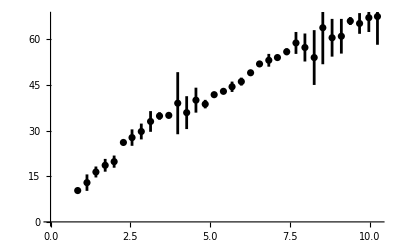

```mathematica
ErrorPlot=ErrorListPlot[rvcerr,PlotRange->{{0,rmax},{0,vmax}},PlotStyle->{Thickness[0.005],Black}]
```

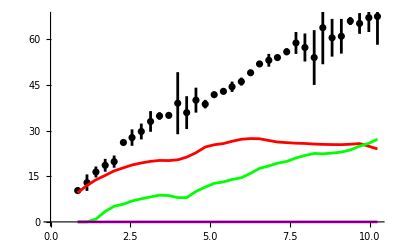

```mathematica
rvcstars=Table[{colx[[i]],vcstars[[i]]},{i,imax}];
rvcgas=Table[{colx[[i]],vcgas[[i]]},{i,imax}];
rvcbul=Table[{colx[[i]],vcbul[[i]]},{i,imax}];
pRCStars=ListPlot[rvcstars,PlotRange->{{0,rmax},{0,vmax}},GridLines->Automatic,PlotStyle->{Thickness[0.005],Red},
Joined->True];
pRCGas=ListPlot[rvcgas,PlotRange->{{0,rmax},{-20,vmax}},GridLines->Automatic,PlotStyle->{Thickness[0.005],Green},
Joined->True];
pRCBulb=ListPlot[rvcbul,PlotRange->{{0,rmax},{0,vmax}},GridLines->Automatic,PlotStyle->{Thickness[0.005],Magenta},
Joined->True];
Show[ErrorPlot,pRCStars,pRCGas,pRCBulb]
```

```mathematica
xyerr=Table[{{colx[[i]],coly[[i]]},ErrorBar[sigma[[i]]]},{i,imax}];
```

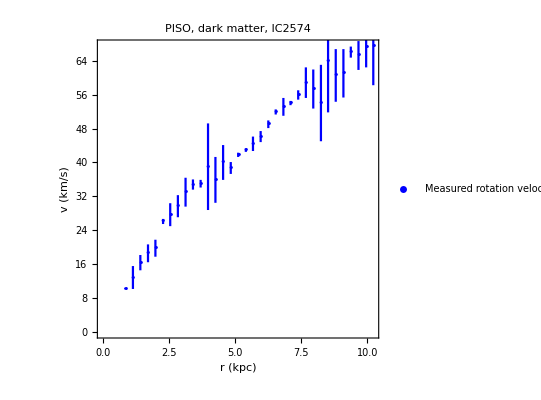

```mathematica
ErrorPlotRC=myErrorListPlot[xyerr,All,xLabelPlotPDF,yLabelPlotPDF,ObsText,{Left,Top},ModelName,{ObsColor},{ObsMarker,pointSize0}]
```

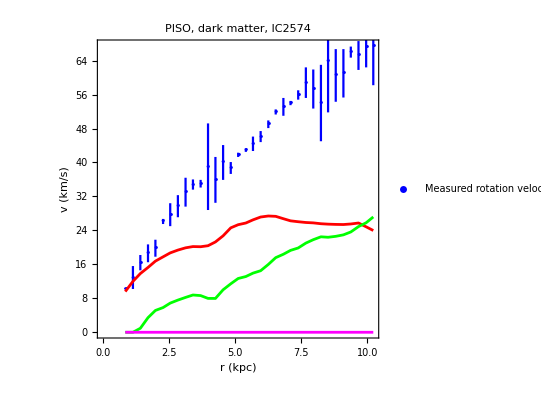

```mathematica
ErrorPlot=Show[ErrorPlotRC,pRCStars,pRCGas,pRCBulb]
```

```mathematica
colx
vcstarsΥ=Sqrt[ΥDisk]*vcstars
vcbulgeΥ=Sqrt[ΥBulge]*vcbul
vcgasΥ=Sqrt[ΥGas]*vcgas
```

{0.85,1.14,1.42,1.71,1.99,2.28,2.55,2.84,3.13,3.41,3.7,3.98,4.26,4.55,4.84,5.12,5.41,5.68,5.97,6.26,6.54,6.83,7.1,7.39,7.68,7.96,8.25,8.52,8.81,9.1,9.38,9.67,9.96,10.23}

{6.78115,8.47821,9.77929,10.7975,11.8511,12.5653,13.2229,13.6896,14.0644,14.2765,14.2482,14.4179,15.0472,16.0655,17.3948,17.9181,18.2009,18.7242,19.1979,19.3677,19.3111,18.9151,18.5616,18.4131,18.2858,18.2221,18.0807,18.01,17.9676,17.9464,18.0383,18.2009,17.5645,16.9493}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.,0.,0.94,3.44,5.14,5.82,6.87,7.58,8.21,8.78,8.64,7.98,7.97,10.01,11.42,12.67,13.13,13.93,14.5,15.98,17.58,18.38,19.29,19.86,21.01,21.81,22.49,22.38,22.6,22.95,23.63,24.89,25.8,27.17}

```mathematica
nBins=200;
```

```mathematica
xOffSet=0.05;
x0=0. ;
xFinal=rmax;
xFinOffSet=0.01;
xFin=xFinal+xFinOffSet
zeroxOffSet=rmin;
```

10.24

```mathematica
dxBin=N[(rmax+xOffSet-rmin)/(nBins-1)];
colxBins=Table[rmin+dxBin*(i-1),{i,nBins}];
```

#### 2. Interpolating observed rotation curve

```mathematica
rvcObs=Table[{colx[[i]],coly[[i]]},{i,imax}]
```

{{0.85,10.3},{1.14,12.9},{1.42,16.4},{1.71,18.6},{1.99,19.8},{2.28,26.1},{2.55,27.7},{2.84,29.7},{3.13,33.},{3.41,34.8},{3.7,35.},{3.98,39.},{4.26,35.9},{4.55,40.},{4.84,38.7},{5.12,41.8},{5.41,42.9},{5.68,44.4},{5.97,46.1},{6.26,49.},{6.54,51.9},{6.83,53.1},{7.1,54.},{7.39,55.9},{7.68,58.8},{7.96,57.3},{8.25,54.},{8.52,63.8},{8.81,60.5},{9.1,61.},{9.38,66.},{9.67,65.2},{9.96,67.1},{10.23,67.5}}

```mathematica
vRCInterp=Interpolation[rvcObs,InterpolationOptions]
```

InterpolatingFunction[…]

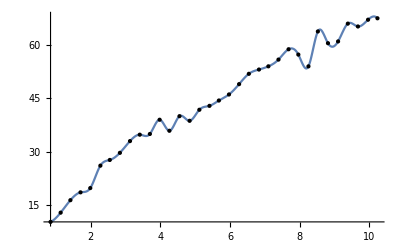

```mathematica
pRCObsInter=Plot[vRCInterp[x],{x,rmin,rmax},Epilog->Map[Point, rvcObs]]
```

#### 3. Interpolating observed rotation curve bulge starts

```mathematica
rvcbulgeΥ=Table[{colx[[i]],vcbulgeΥ[[i]]},{i,imax}]
```

{{0.85,0.},{1.14,0.},{1.42,0.},{1.71,0.},{1.99,0.},{2.28,0.},{2.55,0.},{2.84,0.},{3.13,0.},{3.41,0.},{3.7,0.},{3.98,0.},{4.26,0.},{4.55,0.},{4.84,0.},{5.12,0.},{5.41,0.},{5.68,0.},{5.97,0.},{6.26,0.},{6.54,0.},{6.83,0.},{7.1,0.},{7.39,0.},{7.68,0.},{7.96,0.},{8.25,0.},{8.52,0.},{8.81,0.},{9.1,0.},{9.38,0.},{9.67,0.},{9.96,0.},{10.23,0.}}

```mathematica
vcBulge=Interpolation[rvcbulgeΥ,InterpolationOptions]
```

InterpolatingFunction[…]

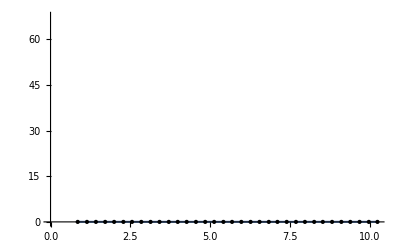

```mathematica
PvcBulge=Plot[vcBulge[x],{x,rmin,rmax},Epilog->Map[Point, rvcbulgeΥ],PlotRange->{{0,rmax},{0,vmax}}]
```

```mathematica
pRCBulbΥ=ListPlot[rvcbulgeΥ,PlotRange->{{0,rmax},{0,vmax}},GridLines->Automatic,PlotStyle->{Thickness[0.005],Magenta},
Joined->True];
```

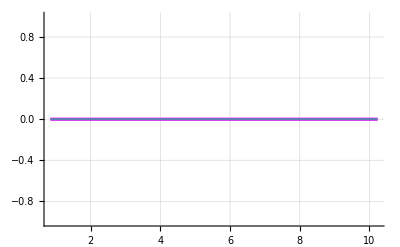

```mathematica
Show[pRCBulb,pRCBulbΥ,PvcBulge,PlotRange->All]
```

#### 4. Interpolating observed rotation curve disc stars

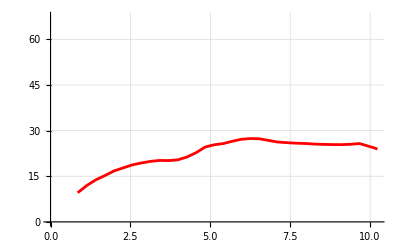

```mathematica
Show[pRCStars]
```

```mathematica
rvcstarsΥ=Table[{colx[[i]],vcstarsΥ[[i]]},{i,imax}]
```

{{0.85,6.78115},{1.14,8.47821},{1.42,9.77929},{1.71,10.7975},{1.99,11.8511},{2.28,12.5653},{2.55,13.2229},{2.84,13.6896},{3.13,14.0644},{3.41,14.2765},{3.7,14.2482},{3.98,14.4179},{4.26,15.0472},{4.55,16.0655},{4.84,17.3948},{5.12,17.9181},{5.41,18.2009},{5.68,18.7242},{5.97,19.1979},{6.26,19.3677},{6.54,19.3111},{6.83,18.9151},{7.1,18.5616},{7.39,18.4131},{7.68,18.2858},{7.96,18.2221},{8.25,18.0807},{8.52,18.01},{8.81,17.9676},{9.1,17.9464},{9.38,18.0383},{9.67,18.2009},{9.96,17.5645},{10.23,16.9493}}

```mathematica
pRCStarsΥ=ListPlot[rvcstarsΥ,PlotRange->{{0,rmax},{0,vmax}},GridLines->Automatic,PlotStyle->{Thickness[0.005],Red},
Joined->True];
```

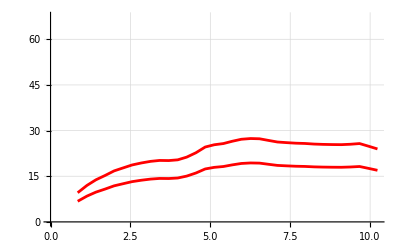

```mathematica
Show[pRCStars,pRCStarsΥ]
```

```mathematica
vcDisc=Interpolation[rvcstarsΥ,InterpolationOptions]
```

InterpolatingFunction[…]

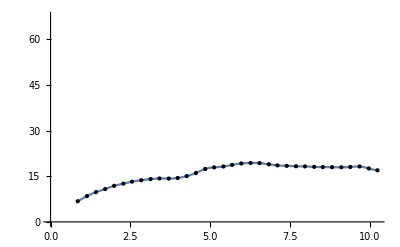

```mathematica
PvcDisc=Plot[vcDisc[x],{x,rmin,rmax}, Epilog->Map[Point, rvcstarsΥ],PlotRange->{{0,rmax},{0,vmax}}]
```

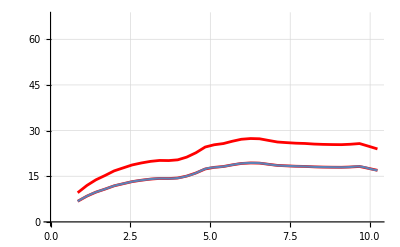

```mathematica
Show[pRCStars,pRCStarsΥ,PvcDisc]
```

#### 5. Interpolating observed rotation curve gas

```mathematica
rvcgasΥ=Table[{colx[[i]],vcgasΥ[[i]]},{i,imax}]
```

{{0.85,0.},{1.14,0.},{1.42,0.94},{1.71,3.44},{1.99,5.14},{2.28,5.82},{2.55,6.87},{2.84,7.58},{3.13,8.21},{3.41,8.78},{3.7,8.64},{3.98,7.98},{4.26,7.97},{4.55,10.01},{4.84,11.42},{5.12,12.67},{5.41,13.13},{5.68,13.93},{5.97,14.5},{6.26,15.98},{6.54,17.58},{6.83,18.38},{7.1,19.29},{7.39,19.86},{7.68,21.01},{7.96,21.81},{8.25,22.49},{8.52,22.38},{8.81,22.6},{9.1,22.95},{9.38,23.63},{9.67,24.89},{9.96,25.8},{10.23,27.17}}

```mathematica
vcGas=Interpolation[rvcgasΥ,InterpolationOptions]
```

InterpolatingFunction[…]

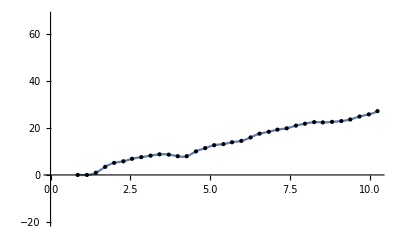

```mathematica
PvcGas=Plot[vcGas[x],{x,rmin,rmax},Epilog->Map[Point, rvcgasΥ],PlotRange->{{0,rmax},{-20,vmax}}]
```

```mathematica
pRCGasΥ=ListPlot[rvcgasΥ,PlotRange->{{0,rmax},{-20,vmax}},GridLines->Automatic,PlotStyle->{Thickness[0.005],Green},
Joined->True];
```

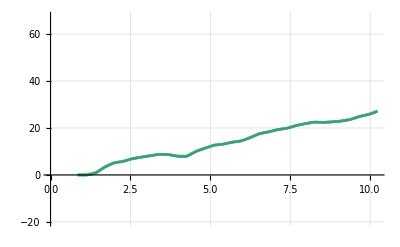

```mathematica
Show[pRCGas,pRCGasΥ,PvcGas]
```

#### 6. LATEX and Tables

```mathematica
cadenaJoinTeX=StringJoin[cadena0TeX,cadena1,cadena2,underLinStr,cadenaName,extTeX];
cadenaJoinTXT=StringJoin[cadena0TXT,cadena1,cadena2,underLinStr,cadenaName,extTXT];
```

```mathematica
cadenaJoinVCPDF=StringJoin[cadena0PDF,"rc",cadena1,cadena2,cadenaName,extPDF];
```

```mathematica
cadenaJoinCadenas1=StringJoin[cadena0Cadenas1,cadena1,cadena2,underLinStr,cadenaName,cadenaMC1,extTXT]
cadenaJoinCadenas2=StringJoin[cadena0Cadenas2,cadena1,cadena2,underLinStr,cadenaName,cadenaMC2,extTXT]
```

Results/Chains/IC2574_PISO-MC1.txt

Results/Chains/IC2574_PISO-MC2.txt

```mathematica
cadenaJoinCadenasExt=StringJoin[cadena0Cadenas1,cadena1,cadena2,underLinStr,cadenaName,cadenaMCExt,extTXT];
cadenaJoinCadenasMin=StringJoin[cadena0Cadenas1,cadena1,cadena2,underLinStr,cadenaName,cadenaMCMin,extTXT];
```

```mathematica
fileNameLaTeX=FileNameJoin[{cadenaJoinTeX}]
fileNameTXT=FileNameJoin[{cadenaJoinTXT}]
```

Results/LaTeX/IC2574_PISO.tex

Results/TXT/IC2574_PISO.txt

```mathematica
ModelNameTeX=StringJoin["(",GalaxyNumberTeX,")\ ",cadena1,"\ ",cadena2];
```

```mathematica
(*column 1*)
ModelNameTXT=StringJoin[cadena1,cadena2];
```

```mathematica
fileNamePlotRCsPDF=FileNameJoin[{cadenaJoinVCPDF}];
```

```mathematica
FrameLabelPlotRCsPDF=StringJoin[cadena1," ",cadena2,ModelNamePlotPDF];
```

```mathematica
cadenaJoinPDFModelChi2=StringJoin[cadena0PDF,cadena1,cadena2,underLinStr,cadenaName,underLinStr,"Chi2",extPDF];
fileNamePDFModelChi2=FileNameJoin[cadenaJoinPDFModelChi2]
cadenaJoinTableModelChi2=StringJoin[cadena0Tables,cadena1,cadena2,underLinStr,ModelText,underLinStr,"Chi2",extDAT];
fileNameTableModelChi2=FileNameJoin[cadenaJoinTableModelChi2]
```

Results/PDF/IC2574_PISO_Chi2.pdf

Results/Tables/IC2574_PISO_Chi2.dat

```mathematica
cadenaJoinPDFModelMCMC=StringJoin[cadena0PDF,cadena1,cadena2,underLinStr,ModelText,underLinStr,"MCMC",extPDF];
fileNamePDFModelMCMC=FileNameJoin[cadenaJoinPDFModelMCMC]
```

Results/PDF/IC2574_PISO_MCMC.pdf

```mathematica
cadenaJoinTableModelMCMC=StringJoin[cadena0Tables,cadena1,cadena2,underLinStr,ModelText,underLinStr,"MCMC",extDAT]
fileNameTableModelMCMC=FileNameJoin[cadenaJoinTableModelMCMC];
```

Results/Tables/IC2574_PISO_MCMC.dat

#### 7. LATEX paramnames to use with GetDist

```mathematica
(* 
col1: weights, 
col2: -2LogLike, 
col3: ρs (p1);
col4: rs (p2);
col5: muDM (p3);
col6: m300 (p4);
col7: mTot (DM) (p5);
col8: %mTot (DM) (p6)
*)
```

```mathematica
cadenaJoinCadenasParamnames=StringJoin[cadena0Cadenas1,cadena1,cadena2,underLinStr,cadenaName,"-MC",".paramnames"];
```

```mathematica
(*Fit parameters*)
lineTeXparam1=Row[Table[{"p1","    \\rho_s"} ]];
lineTeXparam2=Row[Table[{"p2","      r_s"} ]];
```

```mathematica
(*Derived quantities (with an asterisk)*)
lineTeXparam3=Row[Table[{"p3*","    \\mu_{DM}"} ]];
lineTeXparam4=Row[Table[{"p4*","      m_{300}"} ]];
lineTeXparam5=Row[Table[{"p5*","    m_{DM}"} ]];
lineTeXparam6=Row[Table[{"p6*","      \\% m_{DM}"} ]];
```

```mathematica
fileNameLaTeXParamSave=StringJoin[cadenaJoinCadenasParamnames];
```

```mathematica
DeleteFile[fileNameLaTeXParamSave];
s=OpenAppend[fileNameLaTeXParamSave]
Do[WriteString[s,lineTeXparam1, "\ \n"]]
Do[WriteString[s,lineTeXparam2, "\ \n"]]
Do[WriteString[s,lineTeXparam3, "\ \n"]]
Do[WriteString[s,lineTeXparam4, "\ \n"]]
Do[WriteString[s,lineTeXparam5, "\ \n"]]
Do[WriteString[s,lineTeXparam6, "\ \n"]]
Close[s]
```

OutputStream[…]

Results/Chains/IC2574_PISO-MC.paramnames

```mathematica
cadenaJoinCadenasParamnamesExt=StringJoin[cadena0Cadenas1,cadena1,cadena2,underLinStr,cadenaName,"-MC","Ext",".paramnames"];
commandstringCopy="cp "<>fileNameLaTeXParamSave<>" "<>cadenaJoinCadenasParamnamesExt;
Run[commandstringCopy]
```

0

## 5. Fitting using min χ^2

```mathematica
Timing[fit=fitChi2Fun[colx,coly,sigma,imax,fitPar,ymodel,{parametersPriors},optFitChi]]
```

{0.098346,{90.8314,{p1→219.37,p2→6.15492}}}

```mathematica
reglasminχ2=fit[[2]]
ChiRedFit=fit[[1]]/(imax-np)
```

{p1→219.37,p2→6.15492}

2.83848

```mathematica
reglasminχ2=Join[Table[fit[[2,i]],{i,np}],{χ2red->fit[[1]]/(imax-np)}]
```

{p1→219.37,p2→6.15492,χ2red→2.83848}

```mathematica
(*P and Q values*)
CDF[ChiSquareDistribution[imax-np],fit[[1]]]
QSN=1-CDF[ChiSquareDistribution[imax-np],fit[[1]]]
```

1.

1.53287×10^-7

```mathematica
(*If you have more parameters add lines as needed*)
fitPar[[1]] ρFactor/.reglasminχ2 (*in solar masses per pc cubic*)
fitPar[[2]]/.reglasminχ2 (*in kpc*)
```

0.00405914

6.15492

```mathematica
fit[[1]]
```

90.8314

```mathematica
fitModel=Evaluate[chi2[colx,coly,sigma,imax,fitPar,ymodel]/.reglasminχ2]
```

90.8314

```mathematica
fitParSuplement={}/.reglasminχ2
fitParFix=Join[{p1,p2},fitParSuplement]
```

{}

{p1,p2}

```mathematica
pFitTable={};
Do[
AppendTo[pFitTable,fitPar[[i]]/.reglasminχ2]
,{i,np}]
```

{1.67076,Null}

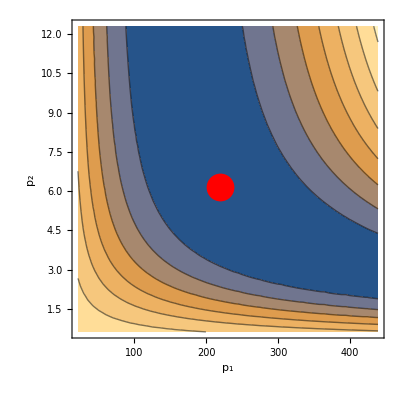

```mathematica
p2Dpoint=Graphics[{Red,PointSize[0.05],Point[{pFitTable[[1]],pFitTable[[2]]}]}];
Timing[pContourchi2=ContourPlot[Evaluate[chi2Fun[colx,coly,sigma,imax,fitParFix,ymodel]-fitModel],{p1,0.1*pFitTable[[1]],2*pFitTable[[1]]},{p2,0.1*pFitTable[[2]],2*pFitTable[[2]]},AxesLabel->{"p_1","p_2","χ^2-(χ^2)_min"}];]
Show[pContourchi2,p2Dpoint]
```

```mathematica
(*Computation of derived useful quantities (especific for galactic rotation curves)*)
```

```mathematica
MassDM=mDM[rmax,fitPar]mFactor /.reglasminχ2
```

7.5277×10^9

```mathematica
MassGas=rmax (vcGas[rmax])^2 mFactor
MassDisk=rmax (vcDisc[rmax])^2 mFactor
MassBulg=rmax (vcBulge[rmax])^2 mFactor
```

1.75599×10^9

6.83358×10^8

0.

```mathematica
MassTotal=MassGas+MassDisk+MassBulg+MassDM
MassBarions=MassGas+MassDisk+MassBulg
```

9.96704×10^9

2.43935×10^9

```mathematica
MassPGas=100 MassGas/MassTotal
MassPDisk=100 MassDisk/MassTotal
MassPBulge=100 MassBulg/MassTotal
```

17.6179

6.85618

0.

```mathematica
MassPBarions=100 MassBarions/MassTotal
MassPDM=100 MassDM/MassTotal
```

24.4741

75.5259

## 6. Plotting (min χ^2 results and produce xyz table of the model)...

```mathematica
reglasminχ2
```

{p1→219.37,p2→6.15492,χ2red→2.83848}

```mathematica
pmodel1Chi2=myPlotG[Evaluate[ymodel[t,fitPar]/.reglasminχ2],t,x0+zeroxOffSet,xFinal,All,xLabelPlotPDF,yLabelPlotPDF,modelNameChi2,modelPlace,"",{modelLineType,lineThickness3,chi2Color}];
pmodel1=Show[ErrorPlot,pmodel1Chi2,PlotRange->All];
```

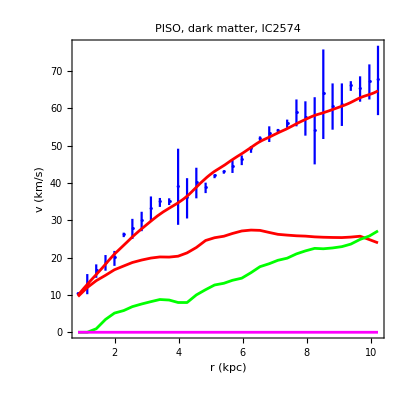

```mathematica
plotAllChi2=Show[pmodel1]
```

```mathematica
Export[fileNamePDFModelChi2,plotAllChi2,"PDF"];
```

```mathematica
prChi2=fitPar/.reglasminχ2
```

{219.37,6.15492}

```mathematica
ModelTableToSaveAll=Table[{colxBins[[i]],
ymodel[colxBins[[i]],prChi2]
},{i,Length[colxBins]}];
Length[ModelTableToSaveAll]
```

200

```mathematica
(*Adapt to your needs*)
strheader1="# "<>ModelName<>", dark matter params:  p1="<>ToString[prChi2[[1]]]<>",   p2="<>ToString[prChi2[[2]]] 
strheader2="# 1. r (kpc), 2. vel (km/s)" 
PrependTo[ModelTableToSaveAll, strheader2];
PrependTo[ModelTableToSaveAll, strheader1];
```

# PISO, dark matter, IC2574, dark matter params:  p1=219.37,   p2=6.15492

# 1. r (kpc), 2. vel (km/s)

```mathematica
Export[fileNameTableModelChi2,ModelTableToSaveAll]
```

Results/Tables/IC2574_PISO_Chi2.dat

## 7. MCMC

### 1. Setting the data

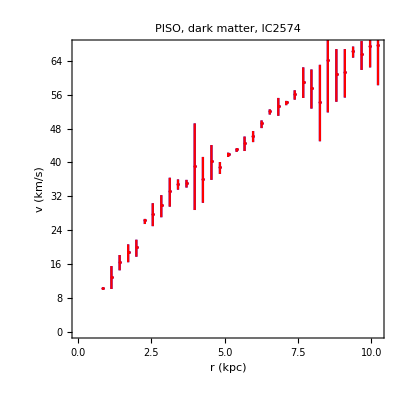

```mathematica
RCData=RCTable[[All,{1,2,3}]];
plt1=myErrorListPlot[RCData,All,xLabelPlotPDF,yLabelPlotPDF,"RCData",{Left,Top},ModelName,{Red},{ObsMarker,pointSize0}];
Show[ErrorPlotRC,plt1]
```

```mathematica
Print["Number of data in the sample : N_Data = ",Length[RCData]," with ",Min[RCData[[All,1]]]," ≤ r ≤ ",Max[RCData[[All,1]]],"."]
```

Number of data in the sample : N_Data = 34 with 0.85 ≤ r ≤ 10.23.

```mathematica
fileNameMC1=FileNameJoin[{cadenaJoinCadenas1}];
fileNameMC2=FileNameJoin[{cadenaJoinCadenas2}];
fileNameMCExt=FileNameJoin[{cadenaJoinCadenasExt}];
fileNameMCMin=FileNameJoin[{cadenaJoinCadenasMin}];
```

```mathematica
ProductRC=Product[RCData[[is,3]]^2,{is,1,Length[RCData]}]
(*Product of sigma^2*)
```

4.51573×10^21

### 2. Setting wide range for parameters (priors)

```mathematica
(*Setting wide range for the parameters*)
```

```mathematica
pFitTable
```

{219.37,6.15492}

```mathematica
prL={};
prU={};
prG={};
Do[
pLtmp=0.5*pFitTable[[i]];
pUtmp=1.5*pFitTable[[i]];
pGtmp=pFitTable[[i]];
AppendTo[prL,pLtmp];
AppendTo[prU,pUtmp];
AppendTo[prG,pGtmp];
,{i,np}]
```

```mathematica
prL=parLPriors
prU=parUPriors
```

{0,0}

{10000,100}

```mathematica
prG
```

{219.37,6.15492}

```mathematica
CalcTmp=ComputeLikeF[prG,RCData,ymodel,np,ProductRC];
ChiRCRedInit=CalcTmp[[2]];
```

```mathematica
Do[
Print["Guess Model Parameters : pG[",i,"] = ",
prG[[i]]]
,{i,np}]
```

Guess Model Parameters : pG[1] = 219.37

Guess Model Parameters : pG[2] = 6.15492

```mathematica
Print["Overall Fit Quality : χ_red^2 = ",ChiRCRedInit]
```

Overall Fit Quality : χ_red^2 = 2.83848

```mathematica
ChiRCRedInit=1000;
jntExt=1;
Timing[
While[(ChiRCRedInit>10 && jntExt<ntrialsExt),
SortTabGuess=MakeChainWideRange[prL,prU,RCData,vcT,np,ntrials,ProductRC];

prG={};
Do[
AppendTo[prG,SortTabGuess[[i]]];
,{i,np}];

CalcTmp=ComputeLike[prG,RCData,vcT,np,ProductRC];
ChiRCRedInit=CalcTmp[[2]];
jntExt++;
];
]
jntExt
```

{0.382104,Null}

9

```mathematica
Do[
Print["Guess Model Parameters : pG[",i,"] = ",
prG[[i]]]
,{i,np}]
```

Guess Model Parameters : pG[1] = 126.588

Guess Model Parameters : pG[2] = 63.125

```mathematica
Print["Overall Fit Quality : χ_red^2 = ",ChiRCRedInit,"."]
```

Overall Fit Quality : χ_red^2 = 9.47124.

```mathematica
(*A good start is Chi2 < 10*)
```

```mathematica
Do[
prtmp=prU[[i]];
If[prU[[i]]<prL[[i]],prU[[i]]=prL[[i]];prL[[i]]=prtmp]
,{i,np}]
```

```mathematica
prStep={};
Do[
AppendTo[prStep,N[(prU[[i]]-prL[[i]])/nmc]];
,{i,np}];
```

```mathematica
prStep
```

{10.,0.1}

```mathematica
prL
prU
```

{0,0}

{10000,100}

```mathematica
prL=parLPriors
prU=parUPriors
```

{0,0}

{10000,100}

```mathematica
prStep={};
Do[
AppendTo[prStep,N[(prU[[i]]-prL[[i]])/nmc]];
,{i,np}];
```

```mathematica
prStep
```

{10.,0.1}

### 3. Running MCMC

```mathematica
If[nth==1,nc=nc1,nc=nc2];
```

```mathematica
(*Chain 1: *)
If[nth==1,TabChain={},TabChain=Import[fileNameMC1,"Table"]];
If[nth==1,TabStartOne=Table[RandomReal[{0.99,1.01}]*prG[[i]],{i,np}],TabStartOne=Table[TabChain[[Length[TabChain],i]],{i,np}]];
Timing[MakeChainF[prL,prU,prStep,
nc,δ,TabStartOne,TabChain,RCData,vcT,np,fileNameMC1,ProductRC];]
```

814.463 203.979 -305.242 10000 random walks completed...

228.42 204.304 -12.0581 20000 random walks completed...

243.689 204.303 -19.693 30000 random walks completed...

{18.7322,Null}

```mathematica
(*Chain 2: *)
If[nth==1,TabChain={},TabChain=Import[fileNameMC2,"Table"]];
If[nth==1,TabStartTwo=Table[RandomReal[{0.99,1.01}]*prG[[i]],{i,np}],TabStartTwo=Table[TabChain[[Length[TabChain],i]],{i,np}]];
Timing[MakeChainF[prL,prU,prStep,
nc,δ,TabStartTwo,TabChain,RCData,vcT,np,fileNameMC2,ProductRC];]
```

227.386 204.094 -11.6459 10000 random walks completed...

427.572 204.32 -111.626 20000 random walks completed...

289.304 204.167 -42.5685 30000 random walks completed...

{18.6814,Null}

### 4. Importing and plotting the chain

```mathematica
(*Importing and plotting the chain*)
```

```mathematica
Timing[MCProc1=MarkovChainProcessing1[fileNameMC1,fileNameMC2,np];
prMCMCBF=Table[MCProc1[[1,i]],{i,np}];
ChiLikeBF=MCProc1[[1,np+1]];
TabGR=MCProc1[[2]];
TabChainFull=MCProc1[[3]];
CalcTmp=ComputeLikeF[prMCMCBF,RCData,ymodel,np,ProductRC];
ChiRCRedMCMC=CalcTmp[[2]];]
```

{3.04509,Null}

```mathematica
ChiLikeBF (* -2 log(like) *)
```

203.181

```mathematica
Print["Gelmann - Rubin Convergence Test : R = ",N[TabGR],"."]
Print["Number of points in the coadded chain before burn in cut and thinning : N_full = ",Length[TabChainFull],"."]
```

Gelmann - Rubin Convergence Test : R = {1.00031,1.00002}.

Number of points in the coadded chain before burn in cut and thinning : N_full = 60000.

```mathematica
Do[
Print["Best Fit Model Parameters : prMCMCBF[",i,"] = ",
prMCMCBF[[i]]]
,{i,np}]
```

Best Fit Model Parameters : prMCMCBF[1] = 219.424

Best Fit Model Parameters : prMCMCBF[2] = 6.15436

```mathematica
Print["Overall Fit Quality : χ_red^2 = ",ChiRCRedMCMC,"."]
```

Overall Fit Quality : χ_red^2 = 2.83849.

```mathematica
reglasMCMC1=Join[Table[fitPar[[i]]->prMCMCBF[[i]],{i,np}],{χ2red->ChiRCRedMCMC}]
```

{p1→219.424,p2→6.15436,χ2red→2.83849}

```mathematica
(*Processing histograms of the parameters after burning (BurnFrac) and thinning (NThin) and extracting constrains on the parameters*)
```

```mathematica
Timing[MCProc2=MarkovChainProcessing2[fileNameMC1,fileNameMC2,np,NThin,BurnFrac];] (*30% burning and thinning 10*)
ChBest=MCProc2[[1]];
TabChain=MCProc2[[2]];
```

{0.557422,Null}

```mathematica
hTable=Join[Table[{Histogram[TabChain[[All,i]],Automatic,"PDF",LabelStyle->{"Symbol",10},Frame->True,FrameLabel->{"p_i", "P(p_i)"},Axes->False,PlotRange->All],SmoothHistogram[TabChain[[All,i]],Automatic,"PDF",PlotRange->All]},{i,np}],{{Histogram[TabChain[[All,np+1]],Automatic,"PDF",LabelStyle->{"Symbol",10},Frame->True,FrameLabel->{"-2 ln L", "P(-2 ln L)"},Axes->False,PlotRange->All],SmoothHistogram[TabChain[[All,np+1]],Automatic,"PDF",PlotRange->All]}}];
```

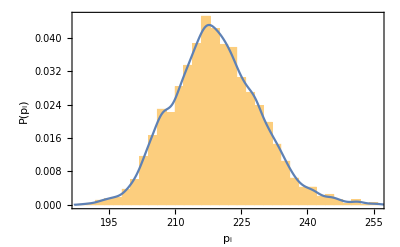
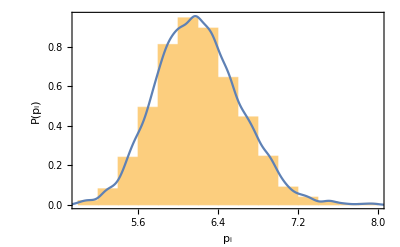
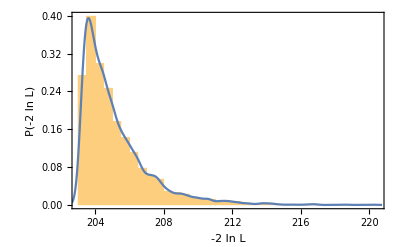

```mathematica
phTable=Table[Show[hTable[[i]]],{i,np+1}]
```

```mathematica
prMCMCBF=Table[ChBest[[i]],{i,np}]
```

{219.424,6.15436}

```mathematica
TabSol=TabChain;
```

```mathematica
CalcTmp=ComputeLikeF[prMCMCBF,RCData,ymodel,np,ProductRC];
ChiRCRedMCMC=CalcTmp[[2]];
```

```mathematica
reglasMCMC2=Join[Table[fitPar[[i]]->prMCMCBF[[i]],{i,np}],{χ2red->ChiRCRedMCMC}]
```

{p1→219.424,p2→6.15436,χ2red→2.83849}

```mathematica
(*Confidence intervals calculation for the parameters:*)
pM=Table[Mean[TabSol[[All,i]]],{i,np}];
pB=Table[Quantile[TabSol[[All,i]],0.50],{i,np}];
(*Interval at 1σ*)
p1sL=Table[Quantile[TabSol[[All,i]],Erfc[2^(-1/2)]/2],{i,np}];
p1sU=Table[Quantile[TabSol[[All,i]],1-Erfc[2^(-1/2)]/2],{i,np}];
(*Interval at 2σ*)
p2sL=Table[Quantile[TabSol[[All,i]],Erfc[0.5^(-1/2)]/2],{i,np}];
p2sU=Table[Quantile[TabSol[[All,i]],1-Erfc[0.5^(-1/2)]/2],{i,np}];
```

```mathematica
Print["Number of points in the coadded chain after burn in cut and thinning : N_thin = ",Length[TabChain],"."]
```

Number of points in the coadded chain after burn in cut and thinning : N_thin = 8402.

```mathematica
Do[
Print["Best Fit Model Parameters : prMCMCBF[",i,"] = ",
prMCMCBF[[i]]]
,{i,np}]
```

Best Fit Model Parameters : prMCMCBF[1] = 219.424

Best Fit Model Parameters : prMCMCBF[2] = 6.15436

```mathematica
Print["Constraints from Thinned Chain (",Length[TabSol]," points) : "]
```

Constraints from Thinned Chain (8402 points) :

```mathematica
Do[
Print[
"p[",i,"] : mean = ",pM[[i]],", median = ",pB[[i]],", 1σ = (",p1sL[[i]],", ",p1sU[[i]],"), 2σ = (",p2sL[[i]],", ",p2sU[[i]],");"
]
,{i,np}]
```

p[1] : mean = 219.179, median = 218.758, 1σ = (209.225, 228.757), 2σ = (201.183, 240.156);

p[2] : mean = 6.20139, median = 6.18146, 1σ = (5.78673, 6.62105), 2σ = (5.43507, 7.0785);

```mathematica
(*minus/plus errors*)
δprm=Table[pM[[i]]-p1sL[[i]],{i,np}]
δprp=Table[p1sU[[i]]-pM[[i]],{i,np}]
```

{9.95444,0.414654}

{9.5777,0.419668}

```mathematica
reglasMCMC=Join[Table[fitPar[[i]]->pM[[i]],{i,np}],{χ2red->ChiRCRedMCMC}]
```

{p1→219.179,p2→6.20139,χ2red→2.83849}

```mathematica
CalcTmp=ComputeLikeF[prMCMCBF,RCData,ymodel,np,ProductRC];
ChiRCRedMCMC=CalcTmp[[2]];
reglasMCMCBF=Join[Table[fitPar[[i]]->prMCMCBF[[i]],{i,np}],{χ2red->ChiRCRedMCMC}]
```

{p1→219.424,p2→6.15436,χ2red→2.83849}

```mathematica
CalcTmp=ComputeLikeF[pM,RCData,ymodel,np,ProductRC];
ChiRCRedMCMC=CalcTmp[[2]];
reglasMCMCMean=Join[Table[fitPar[[i]]->pM[[i]],{i,np}],{χ2red->ChiRCRedMCMC}]
```

{p1→219.179,p2→6.20139,χ2red→2.84268}

```mathematica
CalcTmp=ComputeLikeF[pB,RCData,ymodel,np,ProductRC];
ChiRCRedMCMC=CalcTmp[[2]];
reglasMCMCMedian=Join[Table[fitPar[[i]]->pB[[i]],{i,np}],{χ2red->ChiRCRedMCMC}]
```

{p1→218.758,p2→6.18146,χ2red→2.8386}

## 8. Plotting (min χ^2 and MCMC results)...

```mathematica
reglasToUse=reglasMCMCMedian;
```

```mathematica
pFitTableMCMCMedian=fitPar/.reglasMCMCMedian
```

{218.758,6.18146}

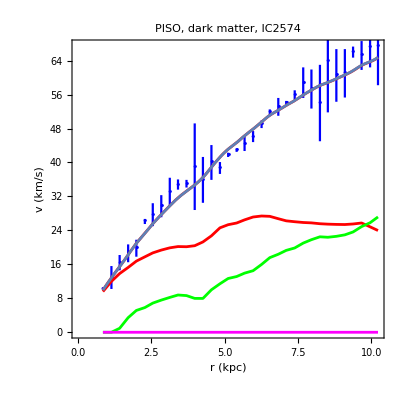

```mathematica
pyModel=myPlotG[Evaluate[ymodel[t,pFitTableMCMCMedian]],t,x0+zeroxOffSet,xFinal,All,xLabelPlotPDF,yLabelPlotPDF,modelNameMCMC,modelPlace,"",{modelLineType,lineThickness3,mcmcColor}];
plotAll=Show[ErrorPlot,pmodel1Chi2,pyModel]
```

## 9. Final processing of the chains

```mathematica
(*Chains in Results/Chains can be processed using GetDist*)
```

#### Cleaning and joining chains

```mathematica
TabChainOne=Import[fileNameMC1,"Table"];
TabChainTwo=Import[fileNameMC2,"Table"];
ncChain1=Length[TabChainOne]
ncChain2=Length[TabChainTwo]
ncChain=ncChain1;
```

30000

30000

```mathematica
maxChainOne1T={};
Do[
AppendTo[maxChainOne1T,Max[TabChainOne[[All,i]]]]
,{i,np}]
maxChainOne1T
minChainOne1T={};
Do[
AppendTo[minChainOne1T,Min[TabChainOne[[All,i]]]]
,{i,np}]
minChainOne1T
```

{255.937,92.0217}

{133.308,4.9885}

```mathematica
maxChainTwo1T={};
Do[
AppendTo[maxChainTwo1T,Max[TabChainTwo[[All,i]]]]
,{i,np}]
maxChainTwo1T
minChainTwo1T={};
Do[
AppendTo[minChainTwo1T,Min[TabChainTwo[[All,i]]]]
,{i,np}]
minChainTwo1T
```

{258.445,62.8157}

{127.311,4.92391}

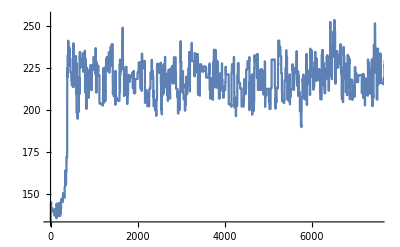
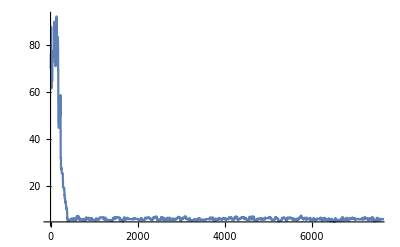

```mathematica
tabChainOnePlots={};
Do[
AppendTo[tabChainOnePlots,ListPlot[TabChainOne[[All,i]],PlotRange->{{0,ncChain/4},{minChainOne1T[[i]],maxChainOne1T[[i]]}},Joined->True]]
,{i,np}]
tabChainOnePlots
```

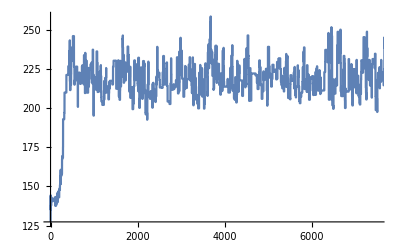
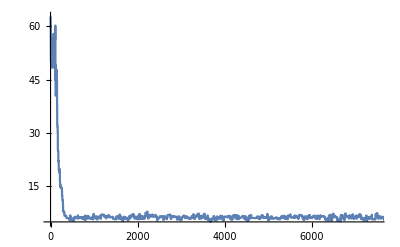

```mathematica
tabChainTwoPlots={};
Do[
AppendTo[tabChainTwoPlots,ListPlot[TabChainTwo[[All,i]],PlotRange->{{0,ncChain/4},{minChainTwo1T[[i]],maxChainTwo1T[[i]]}},Joined->True]]
,{i,np}]
tabChainTwoPlots
```

21001

4201

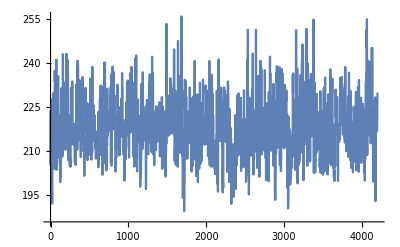
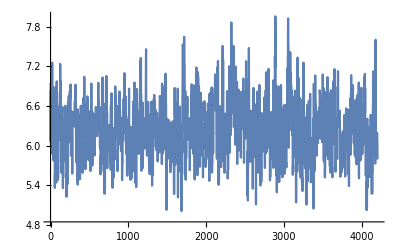

```mathematica
TabChainOneBurn=Table[TabChainOne[[i]],{i,IntegerPart[BurnFrac*ncChain],Length[TabChainOne]}];
Length[TabChainOneBurn]
TabChainOneThin=Table[TabChainOneBurn[[i]],{i,1,Length[TabChainOneBurn],NThin}];
Length[TabChainOneThin]
tabChainOneThinPlots={};
Do[
AppendTo[tabChainOneThinPlots,ListPlot[TabChainOneThin[[All,i]],Joined->True]]
,{i,np}]
tabChainOneThinPlots
```

21001

4201

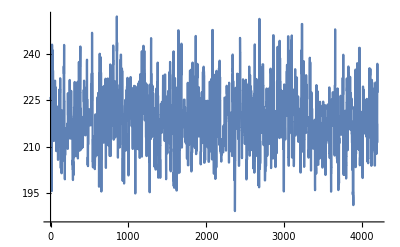
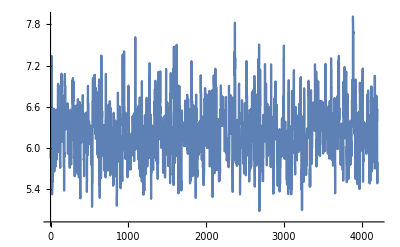

```mathematica
TabChainTwoBurn=Table[TabChainTwo[[i]],{i,IntegerPart[BurnFrac*ncChain],Length[TabChainTwo]}];
Length[TabChainTwoBurn]
TabChainTwoThin=Table[TabChainTwoBurn[[i]],{i,1,Length[TabChainTwoBurn],NThin}];
Length[TabChainTwoThin]
tabChainTwoThinPlots={};
Do[
AppendTo[tabChainTwoThinPlots,ListPlot[TabChainTwoThin[[All,i]],Joined->True]]
,{i,np}]
tabChainTwoThinPlots
```

```mathematica
TabChain=Join[TabChainOneThin,TabChainTwoThin];
ChBest=First[Sort[TabChain,#1[[np+1]]<#2[[np+1]]&]]
Length[TabChain]
```

{219.424,6.15436,203.181}

8402

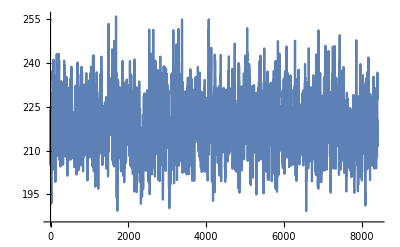
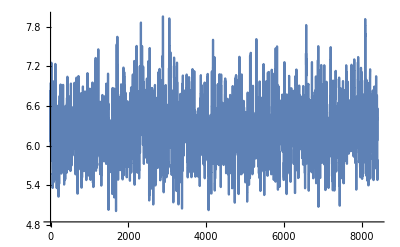

```mathematica
tabChainPlots={};
Do[
AppendTo[tabChainPlots,ListPlot[TabChain[[All,i]],Joined->True]]
,{i,np}]
tabChainPlots
```

#### Computing derived quantities

```mathematica
(*BEGIN : QUANTITIES : RC TWO PARAMETERS MODEL*)
```

```mathematica
ρsChain=TabChain[[All,1]] ρFactor;
```

```mathematica
rsChain=TabChain[[All,2]];
```

```mathematica
muChain=ρsChain*rsChain kilo;
```

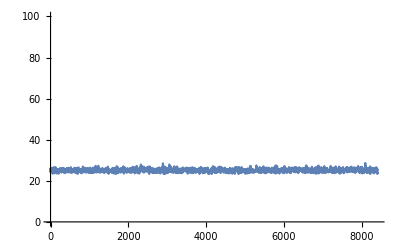

```mathematica
ListPlot[muChain,Joined->True,PlotRange->{0,100}]
```

```mathematica
(*END : QUANTITIES : RC TWO PARAMETERS MODEL*)
```

```mathematica
TabChainTable=Table[Table[TabChain[[All,i]][[j]],{i,np}],{j,Length[TabChain]}];
```

```mathematica
m300Chain=ParallelTable[mDM[0.3,TabChainTable[[i]]] mFactor,{i,Length[TabChain]}];
```

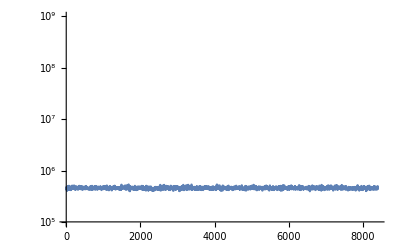

```mathematica
ListLogPlot[m300Chain,Joined->True,PlotRange->{10^5,10^9}]
```

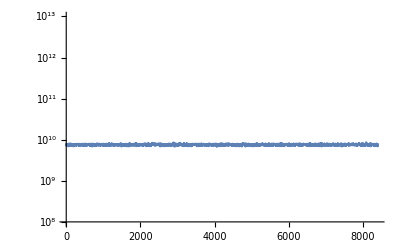

```mathematica
mTotChain=ParallelTable[mDM[rmax,TabChainTable[[i]]] mFactor,{i,Length[TabChain]}];
ListLogPlot[mTotChain,Joined->True,PlotRange->{10^8,10^13}]
```

```mathematica
(*Computing the % of DM mass*)
```

```mathematica
MassBarionsChain=ParallelTable[MassBarions,{i,Length[TabChain]}];
```

```mathematica
MassTotalChain=MassBarionsChain+mTotChain;
```

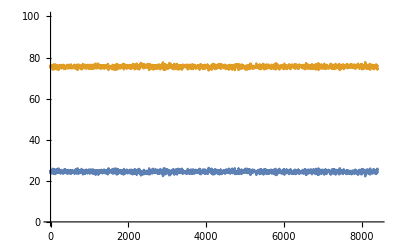

```mathematica
MassPBarionsChain=100 MassBarionsChain/MassTotalChain;
MassPDMChain=100 mTotChain/MassTotalChain;
ListPlot[{MassPBarionsChain,MassPDMChain},Joined->True,PlotRange->{0,100}]
```

```mathematica
(*END of Computing the % of DM mass*)
```

```mathematica
wChain=ParallelTable[1,{i,Length[TabChain]}];
```

```mathematica
(* weights, -2LogLike, ρs, rs, muDM, m300, mTot, %mDM
*)
```

```mathematica
(*8 columnas*)
```

```mathematica
TabChainExt=ParallelTable[{wChain[[i]],
TabChain[[All,np+1]][[i]],
ρsChain[[i]],
rsChain[[i]],
muChain[[i]],
m300Chain[[i]],
mTotChain[[i]],
MassPDMChain[[i]]},
{i,Length[TabChain]}];
```

```mathematica
TabChainMin=ParallelTable[{wChain[[i]],
TabChain[[All,np+1]][[i]],
ρsChain[[i]],rsChain[[i]]},{i,Length[TabChain]}];
```

```mathematica
Export[fileNameMCExt,TabChainExt,"Table"];
Export[fileNameMCMin,TabChainMin,"Table"];
```

```mathematica
(*
Chain in file:
fileNameMCExt
can be processed using GetDist:

$ jupyter notebook

and in the web browser open file "getdist-plots_and_stat.ipynb" and run the notebook.
*)
```

```mathematica
(*Chain table in code units*)
codeUnitsTable={1.0/ρFactor,1.0,1.0,1.0,1.0,1.0};
```

#### Computing mean and error values

```mathematica
(*Only need to add as many parameter sections like the ones with the comment line:
"Computation of confidence interval for parameter (col3==p1):"
 *)
```

```mathematica
(* 
col1: weights, 
col2: -2LogLike, 
col3: ρs, OK,
col4: rs, OK,
col5: muDM, OK,
col6: m300, OK,
col7: mTot (DM) OK,
col8: %mTot (DM) OK
*)
```

```mathematica
(*Computation of confidence interval for parameter (col3==p1):*)
parCol=3;
MCMCMean=Mean[TabChainExt[[All,parCol]]];(*Mean*)
MCMCMedian=Quantile[TabChainExt[[All,parCol]],0.50];(*Median*)
(*Interval at 1σ*)
MCMC1sL=Quantile[TabChainExt[[All,parCol]],Erfc[2^(-1/2)]/2];
MCMC1sU=Quantile[TabChainExt[[All,parCol]],1-Erfc[2^(-1/2)]/2];
(*Interval at 2σ*)
MCMC2sL=Quantile[TabChainExt[[All,parCol]],Erfc[0.5^(-1/2)]/2];
MCMC2sU=Quantile[TabChainExt[[All,parCol]],1-Erfc[0.5^(-1/2)]/2];

col3Mean=MCMCMean;
col3Median=MCMCMedian;
δcol3m=MCMCMedian-MCMC1sL;
δcol3p=MCMC1sU-MCMCMedian;
δcol3SD=StandardDeviation[TabChainExt[[All,parCol]]];
δcol3Median=Quantile[Abs[TabChainExt[[All,parCol]]-MCMCMedian],0.50];

Print["p_1 : mean = ",col3Mean,", median = ",col3Median,";"]
Print["1σ = (",MCMC1sL,", ",MCMC1sU,");"]
Print["2σ = (",MCMC2sL,", ",MCMC2sU,");"]
Print["δ_m = ",δcol3m,", δ_p = ",δcol3p,";"]
Print["δ_Median = ",δcol3Median,", δ_Mean = ",δcol3SD,
";"]
```

p_1 : mean = 0.00405561, median = 0.00404781;

1σ = (0.00387142, 0.00423283);

2σ = (0.00372262, 0.00444376);

δ_m = 0.000176397, δ_p = 0.000185018;

δ_Median = 0.000119646, δ_Mean = 0.000181257;

```mathematica
(*Computation of confidence interval for parameter (col4==p2):*)
parCol=4;
MCMCMean=Mean[TabChainExt[[All,parCol]]];(*Mean*)
MCMCMedian=Quantile[TabChainExt[[All,parCol]],0.50];(*Median*)
(*Interval at 1σ*)
MCMC1sL=Quantile[TabChainExt[[All,parCol]],Erfc[2^(-1/2)]/2];
MCMC1sU=Quantile[TabChainExt[[All,parCol]],1-Erfc[2^(-1/2)]/2];
(*Interval at 2σ*)
MCMC2sL=Quantile[TabChainExt[[All,parCol]],Erfc[0.5^(-1/2)]/2];
MCMC2sU=Quantile[TabChainExt[[All,parCol]],1-Erfc[0.5^(-1/2)]/2];

col4Mean=MCMCMean;
col4Median=MCMCMedian;
δcol4m=MCMCMedian-MCMC1sL;
δcol4p=MCMC1sU-MCMCMedian;
δcol4SD=StandardDeviation[TabChainExt[[All,parCol]]];
δcol4Median=Quantile[Abs[TabChainExt[[All,parCol]]-MCMCMedian],0.50];

Print["p_2 : mean = ",col4Mean,", median = ",col4Median,";"]
Print["1σ = (",MCMC1sL,", ",MCMC1sU,");"]
Print["2σ = (",MCMC2sL,", ",MCMC2sU,");"]
Print["δ_m = ",δcol4m,", δ_p = ",δcol4p,";"]
Print["δ_Median = ",δcol4Median,", δ_Mean = ",δcol4SD,
";"]
```

p_2 : mean = 6.20139, median = 6.18146;

1σ = (5.78673, 6.62105);

2σ = (5.43507, 7.0785);

δ_m = 0.394726, δ_p = 0.439595;

δ_Median = 0.28259, δ_Mean = 0.421158;

```mathematica
(*Computation of confidence interval for parameter (col5==p3):*)
parCol=5;
MCMCMean=Mean[TabChainExt[[All,parCol]]];(*Mean*)
MCMCMedian=Quantile[TabChainExt[[All,parCol]],0.50];(*Median*)
(*Interval at 1σ*)
MCMC1sL=Quantile[TabChainExt[[All,parCol]],Erfc[2^(-1/2)]/2];
MCMC1sU=Quantile[TabChainExt[[All,parCol]],1-Erfc[2^(-1/2)]/2];
(*Interval at 2σ*)
MCMC2sL=Quantile[TabChainExt[[All,parCol]],Erfc[0.5^(-1/2)]/2];
MCMC2sU=Quantile[TabChainExt[[All,parCol]],1-Erfc[0.5^(-1/2)]/2];

col5Mean=MCMCMean;
col5Median=MCMCMedian;
δcol5m=MCMCMedian-MCMC1sL;
δcol5p=MCMC1sU-MCMCMedian;
δcol5SD=StandardDeviation[TabChainExt[[All,parCol]]];
δcol5Median=Quantile[Abs[TabChainExt[[All,parCol]]-MCMCMedian],0.50];

Print["p_3 : mean = ",col5Mean,", median = ",col5Median,";"]
Print["1σ = (",MCMC1sL,", ",MCMC1sU,");"]
Print["2σ = (",MCMC2sL,", ",MCMC2sU,");"]
Print["δ_m = ",δcol5m,", δ_p = ",δcol5p,";"]
Print["δ_Median = ",δcol5Median,", δ_Mean = ",δcol5SD,
";"]
```

p_3 : mean = 25.0772, median = 25.0399;

1σ = (24.3886, 25.7341);

2σ = (23.8551, 26.5515);

δ_m = 0.651338, δ_p = 0.694218;

δ_Median = 0.451261, δ_Mean = 0.683228;

```mathematica
(*Computation of confidence interval for parameter (col6==p4):*)
parCol=6;
MCMCMean=Mean[TabChainExt[[All,parCol]]];(*Mean*)
MCMCMedian=Quantile[TabChainExt[[All,parCol]],0.50];(*Median*)
(*Interval at 1σ*)
MCMC1sL=Quantile[TabChainExt[[All,parCol]],Erfc[2^(-1/2)]/2];
MCMC1sU=Quantile[TabChainExt[[All,parCol]],1-Erfc[2^(-1/2)]/2];
(*Interval at 2σ*)
MCMC2sL=Quantile[TabChainExt[[All,parCol]],Erfc[0.5^(-1/2)]/2];
MCMC2sU=Quantile[TabChainExt[[All,parCol]],1-Erfc[0.5^(-1/2)]/2];

col6Mean=MCMCMean;
col6Median=MCMCMedian;
δcol6m=MCMCMedian-MCMC1sL;
δcol6p=MCMC1sU-MCMCMedian;
δcol6SD=StandardDeviation[TabChainExt[[All,parCol]]];
δcol6Median=Quantile[Abs[TabChainExt[[All,parCol]]-MCMCMedian],0.50];

Print["p_4 : mean = ",col6Mean,", median = ",col6Median,";"]
Print["1σ = (",MCMC1sL,", ",MCMC1sU,");"]
Print["2σ = (",MCMC2sL,", ",MCMC2sU,");"]
Print["δ_m = ",δcol6m,", δ_p = ",δcol6p,";"]
Print["δ_Median = ",δcol6Median,", δ_Mean = ",δcol6SD,
";"]
```

p_4 : mean = 458023., median = 457128.;

1σ = (437329., 477970.);

2σ = (420566., 501604.);

δ_m = 19798.7, δ_p = 20842.3;

δ_Median = 13465.1, δ_Mean = 20384.5;

```mathematica
(*Computation of confidence interval for parameter (col7==p5):*)
parCol=7;
MCMCMean=Mean[TabChainExt[[All,parCol]]];(*Mean*)
MCMCMedian=Quantile[TabChainExt[[All,parCol]],0.50];(*Median*)
(*Interval at 1σ*)
MCMC1sL=Quantile[TabChainExt[[All,parCol]],Erfc[2^(-1/2)]/2];
MCMC1sU=Quantile[TabChainExt[[All,parCol]],1-Erfc[2^(-1/2)]/2];
(*Interval at 2σ*)
MCMC2sL=Quantile[TabChainExt[[All,parCol]],Erfc[0.5^(-1/2)]/2];
MCMC2sU=Quantile[TabChainExt[[All,parCol]],1-Erfc[0.5^(-1/2)]/2];

col7Mean=MCMCMean;
col7Median=MCMCMedian;
δcol7m=MCMCMedian-MCMC1sL;
δcol7p=MCMC1sU-MCMCMedian;
δcol7SD=StandardDeviation[TabChainExt[[All,parCol]]];
δcol7Median=Quantile[Abs[TabChainExt[[All,parCol]]-MCMCMedian],0.50];

Print["p_5 : mean = ",col7Mean,", median = ",col7Median,";"]
Print["1σ = (",MCMC1sL,", ",MCMC1sU,");"]
Print["2σ = (",MCMC2sL,", ",MCMC2sU,");"]
Print["δ_m = ",δcol7m,", δ_p = ",δcol7p,";"]
Print["δ_Median = ",δcol7Median,", δ_Mean = ",δcol7SD,
";"]
```

p_5 : mean = 7.54628×10^9, median = 7.54305×10^9;

1σ = (7.30855×10^9, 7.77744×10^9);

2σ = (7.08688×10^9, 8.01527×10^9);

δ_m = 2.34502×10^8, δ_p = 2.34387×10^8;

δ_Median = 1.59439×10^8, δ_Mean = 2.34548×10^8;

```mathematica
(*Computation of confidence interval for parameter (col8==p6):*)
parCol=8;
MCMCMean=Mean[TabChainExt[[All,parCol]]];(*Mean*)
MCMCMedian=Quantile[TabChainExt[[All,parCol]],0.50];(*Median*)
(*Interval at 1σ*)
MCMC1sL=Quantile[TabChainExt[[All,parCol]],Erfc[2^(-1/2)]/2];
MCMC1sU=Quantile[TabChainExt[[All,parCol]],1-Erfc[2^(-1/2)]/2];
(*Interval at 2σ*)
MCMC2sL=Quantile[TabChainExt[[All,parCol]],Erfc[0.5^(-1/2)]/2];
MCMC2sU=Quantile[TabChainExt[[All,parCol]],1-Erfc[0.5^(-1/2)]/2];

col8Mean=MCMCMean;
col8Median=MCMCMedian;
δcol8m=MCMCMedian-MCMC1sL;
δcol8p=MCMC1sU-MCMCMedian;
δcol8SD=StandardDeviation[TabChainExt[[All,parCol]]];
δcol8Median=Quantile[Abs[TabChainExt[[All,parCol]]-MCMCMedian],0.50];

Print["p_6 : mean = ",col8Mean,", median = ",col8Median,";"]
Print["1σ = (",MCMC1sL,", ",MCMC1sU,");"]
Print["2σ = (",MCMC2sL,", ",MCMC2sU,");"]
Print["δ_m = ",δcol8m,", δ_p = ",δcol8p,";"]
Print["δ_Median = ",δcol8Median,", δ_Mean = ",δcol8SD,
";"]
```

p_6 : mean = 75.558, median = 75.5635;

1σ = (74.9757, 76.1241);

2σ = (74.3934, 76.6673);

δ_m = 0.58786, δ_p = 0.560606;

δ_Median = 0.386353, δ_Mean = 0.573507;

```mathematica
Chi2Best=First[Sort[TabChainExt,#1[[np+1]]<#2[[np+1]]&]];
prMCMCBF=Table[Chi2Best[[i]],{i,3,np+2}];
prMCMCBFCodeUnits=Table[prMCMCBF[[i]]*codeUnitsTable[[i]],{i,np}];
CalcTmp=ComputeLikeF[prMCMCBFCodeUnits,RCData,ymodel,np,ProductRC];
ChiRCRedMCMC=CalcTmp[[2]];
reglasMCMCBF={
p1->Chi2Best[[1+2]] ,
p2->Chi2Best[[2+2]],
p3->Chi2Best[[3+2]] ,
p4->Chi2Best[[4+2]] ,
p5->Chi2Best[[5+2]] ,
p6->Chi2Best[[6+2]] ,
χ2red->ChiRCRedMCMC}
Chi2RedBF=reglasMCMCBF[[np+1]];
```

{p1→0.0035024,p2→7.82682,p3→27.4126,p4→395763.,p5→8.21587×10^9,p6→77.1066,χ2red→3.18261}

```mathematica
colsMean={
col3Mean,
col4Mean,
col5Mean,
col6Mean,
col7Mean,
col8Mean
};
colsMeanCodeUnits=Table[colsMean[[i]]*codeUnitsTable[[i]],{i,np}];
CalcTmp=ComputeLikeF[colsMeanCodeUnits,RCData,ymodel,np,ProductRC];
ChiRCRedMCMC=CalcTmp[[2]];
reglasMCMCMean={
p1->col3Mean ,
p2->col4Mean,
p3->col5Mean ,
p4->col6Mean ,
p5->col7Mean ,
p6->col8Mean ,
χ2red->ChiRCRedMCMC};
Chi2RedMean=reglasMCMCMean[[np+4+1]]
```

χ2red→2.84268

```mathematica
prMedian={
col3Median,
col4Median,
col5Median,
col6Median,
col7Median,
col8Median
}
```

{0.00404781,6.18146,25.0399,457128.,7.54305×10^9,75.5635}

```mathematica
δprMedian={
δcol3Median,
δcol4Median,
δcol5Median,
δcol6Median,
δcol7Median,
δcol8Median
}
```

{0.000119646,0.28259,0.451261,13465.1,1.59439×10^8,0.386353}

```mathematica
prMedianCodeUnits=Table[prMedian[[i]]*codeUnitsTable[[i]],{i,np}];
CalcTmp=ComputeLikeF[prMedianCodeUnits,RCData,ymodel,np,ProductRC];
ChiRCRedMCMC=CalcTmp[[2]];
reglasMCMCMedian={
p1->prMedian[[1]] ,
p2->prMedian[[2]],
p3->prMedian[[3]] ,
p4->prMedian[[4]] ,
p5->prMedian[[5]] ,
p6->prMedian[[6]] ,
χ2red->ChiRCRedMCMC};
Chi2RedMedian=reglasMCMCMedian[[np+4+1]]
```

χ2red→2.8386

```mathematica
(* 
col1: weights, 
col2: -2LogLike, 
col3: ρs, OK,
col4: rs, OK,
col5: muDM, OK,
col6: m300, OK,
col7: mTot (DM) OK,
col8: %mTot (DM) OK
*)
```

```mathematica
reglasMedian=reglasMCMCMedian
reglasMedianδ={
δp1->δcol3Median,
δp2->δcol4Median,
δp3->δcol5Median,
δp4->δcol6Median,
δp5->δcol7Median,
δp6->δcol8Median
}
```

{p1→0.00404781,p2→6.18146,p3→25.0399,p4→457128.,p5→7.54305×10^9,p6→75.5635,χ2red→2.8386}

{δp1→0.000119646,δp2→0.28259,δp3→0.451261,δp4→13465.1,δp5→1.59439×10^8,δp6→0.386353}

```mathematica
reglasMean=reglasMCMCMean
reglasMeanδ={
δp1->δcol3SD,
δp2->δcol4SD,
δp3->δcol5SD,
δp4->δcol6SD,
δp5->δcol7SD,
δp6->δcol8SD
}
```

{p1→0.00405561,p2→6.20139,p3→25.0772,p4→458023.,p5→7.54628×10^9,p6→75.558,χ2red→2.84268}

{δp1→0.000181257,δp2→0.421158,δp3→0.683228,δp4→20384.5,δp5→2.34548×10^8,δp6→0.573507}

```mathematica
(*P and Q values*)
PSN=CDF[ChiSquareDistribution[imax-np],χ2red * (imax-np)/.Chi2RedMedian]
QSN=1-PSN
```

1.

1.53083×10^-7

#### Updating arrays

```mathematica
(*Add as many lines as parameters you have*)
```

```mathematica
(* 
col1: weights, 
col2: -2LogLike, 
col3: ρs,
col4: rs,
col5: muDM,
col6: m300,
col7: mTot,
col8: %mTot (DM)
*)
```

```mathematica
reglasToUse=reglasMedian
reglasToUseδ=reglasMedianδ
```

{p1→0.00404781,p2→6.18146,p3→25.0399,p4→457128.,p5→7.54305×10^9,p6→75.5635,χ2red→2.8386}

{δp1→0.000119646,δp2→0.28259,δp3→0.451261,δp4→13465.1,δp5→1.59439×10^8,δp6→0.386353}

```mathematica
pValuesT={};
Do[
AppendTo[pValuesT,fitParExt[[i]]/.reglasToUse]
,{i,npExt}]
pValuesT
```

{0.00404781,6.18146,25.0399,457128.,7.54305×10^9,75.5635}

```mathematica
p1Value=p1/.reglasToUse
p2Value=p2/.reglasToUse
p3Value=p3/.reglasToUse
p4Value=p4/.reglasToUse
p5Value=p5/.reglasToUse
p6Value=p6/.reglasToUse
δp1Value=δp1/.reglasToUseδ
δp2Value=δp2/.reglasToUseδ
δp3Value=δp3/.reglasToUseδ
δp4Value=δp4/.reglasToUseδ
δp5Value=δp5/.reglasToUseδ
δp6Value=δp6/.reglasToUseδ
```

0.00404781

6.18146

25.0399

457128.

7.54305×10^9

75.5635

0.000119646

0.28259

0.451261

13465.1

1.59439×10^8

0.386353

#### Saving parameters in a LATEX file

```mathematica
(*Add as many lines as parameters you have*)
```

```mathematica
(* 
col1: weights, 
col2: -2LogLike, 
col3: ρs,
col4: rs,
col5: muDM,
col6: m300,
col7: mTot,
col8: %mTot (DM)
*)
```

```mathematica
χ2redLatex=SetAccuracy[χ2red/.reglasToUse,digitos]
```

2.839

```mathematica
PSNLaTex=SetAccuracy[PSN,digitos+2]
```

1.

```mathematica
(*BEGIN Model Parameters*)
p1Latex=SetAccuracy[p1Value/(10^-3),digitos]
δp1Latex=SetAccuracy[δp1Value/(10^-3),δdigitos]
p2Latex=SetAccuracy[p2Value,digitos]
δp2Latex=SetAccuracy[δp2Value,δdigitos+δdigitosToAdd]
p3Latex=SetAccuracy[p3Value ,digitos]
δp3Latex=SetAccuracy[δp3Value ,δdigitos+δdigitosToAdd]
p4Latex=SetAccuracy[p4Value/10^7 ,digitos] (*10^7 M_⊙*)
δp4Latex=SetAccuracy[ δp4Value/10^7,δdigitos+δdigitosToAdd] (*10^7 M_⊙*)
p5Latex=SetAccuracy[p5Value/10^10  ,digitos](*10^10 M_⊙*)
δp5Latex=SetAccuracy[δp5Value/10^10 ,δdigitos+δdigitosToAdd] (*10^10 M_⊙*)
p6Latex=SetAccuracy[p6Value ,digitos]
δp6Latex=SetAccuracy[δp6Value ,δdigitos+δdigitosToAdd]
```

4.048

0.12

6.181

0.283

25.04

0.451

0.046

0.001

0.754

0.016

75.564

0.386

#### Saving parameters in a TXT file

```mathematica
(*Add as many lines as parameters you have*)
```

```mathematica
(* 
col1: weights, 
col2: -2LogLike, 
col3: ρs,
col4: rs,
col5: muDM,
col6: m300,
col7: mTot,
col8: %mTot (DM)
*)
```

```mathematica
χ2redTXT=χ2red/.reglasToUse
```

2.8386

```mathematica
PSNTXT=PSN
```

1.

```mathematica
(*BEGIN Model Parameters*)
p1TXT=p1Value/(10^-3)
δp1TXT=δp1Value/(10^-3)
p2TXT=p2Value
δp2TXT=δp2Value
p3TXT=p3Value 
δp3TXT=δp3Value
p4TXT= p4Value/10^7 (*10^7 M_⊙*)
δp4TXT=δp4Value/10^7 (*10^7 M_⊙*)
p5TXT= p5Value/10^10 (*10^10 M_⊙*)
δp5TXT=δp5Value/10^10 (*10^10 M_⊙*)
p6TXT=p6Value 
δp6TXT=δp6Value
```

4.04781

0.119646

6.18146

0.28259

25.0399

0.451261

0.0457128

0.00134651

0.754305

0.0159439

75.5635

0.386353

#### LATEX

```mathematica
(*Add as many lines as parameters you have*)
```

```mathematica
DataTeX=Row[Table[{
p1Latex,"$\\pm$",δp1Latex," & ",
p2Latex,"$\\pm$",δp2Latex," & ",
p3Latex,"$\\pm$",δp3Latex," & ",
p4Latex,"$\\pm$",δp4Latex," & ",
p5Latex,"$\\pm$",δp5Latex," & ",
p6Latex,"$\\pm$",δp6Latex
} ]];
NameData=Row[Table[{ModelNameTeX," & "} ]];
EndData=Row[Table[{χ2redLatex," & ",PSNLaTex, " \\\\"} ]];
AllDataTeX=Row[{NameData,DataTeX," & ",EndData}];
```

```mathematica
fileNameLaTeXSave=StringJoin[fileNameLaTeX]
```

Results/LaTeX/IC2574_PISO.tex

```mathematica
DeleteFile[fileNameLaTeXSave];
s=OpenAppend[fileNameLaTeXSave]
Do[WriteString[s,AllDataTeX, "\ \n"]]
Close[s]
```

OutputStream[…]

Results/LaTeX/IC2574_PISO.tex

#### Tabla TXT

```mathematica
(*Add as many lines as parameters you have*)
```

```mathematica
TabTXTTmp={};
```

```mathematica
(*LumtotTXT=LuminosityGalaxy 
δLumtotTXT=δLuminosityGalaxy *)
```

```mathematica
LumtotTXT=LuminosityGalaxy 
δLumtotTXT=δLuminosityGalaxy
```

1.016

0.012

```mathematica
AppendTo[TabTXTTmp,{GalaxyNumber,ModelNameTXT,
p1TXT,δp1TXT,
p2TXT,δp2TXT,
p3TXT,δp3TXT,
p4TXT,δp4TXT,
p5TXT,δp5TXT,
p6TXT,δp6TXT,
χ2redTXT,PSNTXT,
LumtotTXT, δLumtotTXT}];
```

```mathematica
AppendTo[TabTXTTmp,{}];
```

```mathematica
DeleteFile[fileNameTXT];
```

```mathematica
Export[fileNameTXT,TabTXTTmp,"Table"];
```

## 10. Plotting model and saving its xyz Table

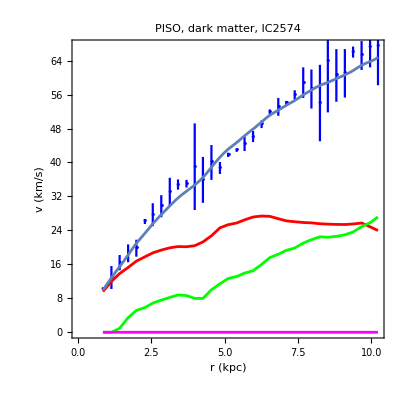

```mathematica
plotAllFinalMCMC=Show[ErrorPlot,pyModel]
```

```mathematica
Export[fileNamePDFModelMCMC,plotAllFinalMCMC,"PDF"];
```

```mathematica
ModelTableToSaveAllMCMC=Table[{colxBins[[i]],
ymodel[colxBins[[i]],prMedian]
},{i,Length[colxBins]}];
Length[ModelTableToSaveAllMCMC]
```

200

```mathematica
(*Adapt to your needs*)
strheader1="# "<>ModelName<>", dark matter params:  p1="<>ToString[prChi2[[1]]]<>",   p2="<>ToString[prChi2[[2]]] 
strheader2="# 1. r (kpc), 2. vel (km/s)" 
PrependTo[ModelTableToSaveAllMCMC, strheader2];
PrependTo[ModelTableToSaveAllMCMC, strheader1];
```

# PISO, dark matter, IC2574, dark matter params:  p1=219.37,   p2=6.15492

# 1. r (kpc), 2. vel (km/s)

```mathematica
Export[fileNameTableModelMCMC,ModelTableToSaveAllMCMC]
```

Results/Tables/IC2574_PISO_MCMC.dat

## 11. Final CPU time of this analysis:

```mathematica
(AbsoluteTime[]-talocal)/60
```

0.8836268

## f.1 Final processing of files

```mathematica
commandstring="cat "<>LaTeXStr<>"/*.tex > "<>rootStrDir<>allTeX
Run[commandstring]
```

cat Results/LaTeX/*.tex > Results/all.tex

0

```mathematica
commandstring="cat "<>TXTStr<>"/*.txt > "<>rootStrDir<>allTXT
Run[commandstring]
```

cat Results/TXT/*.txt > Results/all.txt

0

## f.2 Final all CPU time

```mathematica
(AbsoluteTime[]-taall)/60
```

0.90588745